# Initialization

## Loading functions and definitions

```mathematica
FrontEndTokenExecute["DeleteGeneratedCells"];
(*FrontEndTokenExecute["SelectAll"];
FrontEndTokenExecute["SelectionCloseAllGroups"];*)
(*ClearAll["Global`*"]
ParallelEvaluate[ClearAll["Global`*"]];
CloseKernels[];
LaunchKernels[];*)
LaunchKernels[];
directoryCodes=FileNameJoin[{NotebookDirectory[],"codes/Secondary particles evolution/"}];
inecessary=True;
notev[par_,notebook_]:=If[par,NotebookEvaluate[FileNameJoin[{directoryCodes,notebook}]]]
Print["Load parameters, SM particles properties, thermodynamics functions:"];
Block[{Print=Identity},
notev[inecessary,"parameters-functions.nb"];
];//AbsoluteTiming
Print["Load various cross-sections with muons, pions, kaons:"];
Block[{Print=Identity},
notev[inecessary,"cross-sections.nb"];
];//AbsoluteTiming
Print["Load the solver for the simplified evolution of the Universe:"];
Block[{Print=Identity},
notev[inecessary,"universe-simplified-dynamics.nb"];
];//AbsoluteTiming
Print["Load the dynamics of secondaries in the early universe:"];
Block[{Print=Identity},
notev[inecessary,"evolution-Ys.nb"];
];//AbsoluteTiming
Print["Load the final system and some additional definitions:"];
Block[{Print=Identity},
notev[inecessary,"final-system.nb"];
];//AbsoluteTiming
inecessary=False;
Print["List of metastable particles Y:"]
Yparticleslist
Join[{{"particle","τ [s]", "m [GeV]"}},Table[{particle,lifetime[particle],mass[particle]},{particle,Yparticleslist}]]//Transpose
(*Print[Row[{"Lifetimes in s:"}]];
Join[{{"particle","τ"}},Table[{particle,lifetime[particle]},{particle,particleslist}]]//Transpose
Ttest=10^-3.*3;
Print[Row[{"Annihilation cross-sections <σv> [GeV^-2] at T = ",10^3 Ttest," MeV:"}]];
Join[{{"particle","σ_(ann, tot)"}},Table[{particle,σvAnnTot[particle,Ttest]},{particle,particleslist}]]//Transpose
Print[Row[{"Nuclear cross-sections <σv> [GeV^-2] at T = ",10^3 Ttest," MeV:"}]];
Join[{{"meson","σ_(meson + n -> X)","σ_(meson + n -> p + X)","σ_(meson + p -> X)","σ_(meson + p -> n + X)"}},Table[{particle,σvNuclTot[particle,"n",Ttest],σvConv[particle,"n->p",Ttest],σvNuclTot[particle,"p",Ttest],σvConv[particle,"p->n",Ttest]},{particle,mesonlist}]]
Print["Dynamics of η_B(T) in SBBN:"]
YXtest=0;
mXtest=0.;
τXtest=1.;
ξEMtest=0.;
{nXdyntSBBN[t_],tTdynSBBN[T_],TtdynSBBN[t_],aRatioDyntSBBN[t_],aRatioDynTSBBN[T_],ηBdyntSBBN[t_],ηBdynTSBBN[T_],HtSBBN[t_],HTSBBN[T_]}=Quiet[DynamicsTimeScaleFactor[YXtest,mXtest,τXtest,ξEMtest,tmaxsol]];//AbsoluteTiming
nBSBBN[T_]=ηBdynTSBBN[T]*nγ[T];
LogLogPlot[ηBdynTSBBN[10^-3 T],{T,10^3 TtdynSBBN[tmaxsol],10^3 TiniEM},Frame->True,ImageSize->Large]*)
ClearAll[tIniEM]
SetDirectory[NotebookDirectory[]];
```

Load parameters, SM particles properties, thermodynamics functions:

Identity::argx: Identity called with 9 arguments; 1 argument is expected.

{8.01273,Null}

Load various cross-sections with muons, pions, kaons:

{10.0236,Null}

Load the solver for the simplified evolution of the Universe:

{0.451422,Null}

Load the dynamics of secondaries in the early universe:

{1.46229,Null}

Load the final system and some additional definitions:

{0.196499,Null}

List of metastable particles Y:

{K_L,K^-,K^+,μ^-,μ^+,π^-,π^+}

(particle | K_L | K^- | K^+ | μ^- | μ^+ | π^- | π^+
τ [s] | 5.116×10^-8 | 1.23×10^-8 | 1.23×10^-8 | 2.2×10^-6 | 2.2×10^-6 | 2.6×10^-8 | 2.6×10^-8
m [GeV] | 0.497 | 0.495 | 0.495 | 0.105 | 0.105 | 0.139 | 0.139)

# LLP input

## Description of all the required input

```mathematica
descr1=Table[{Row[{"NtoY[LLP,",t,",m_LLP]"}],Row[{"The number of ",t," particles list per decay of LLP"}]},{t,Yparticleslist}];
descr2={{"nLLPini[LLP,m_LLP,τ_LLP]",Row[{"The number density of the LLP at the temperature T = ",10^3 TiniEM," MeV"}]}};
descr3=Table[{Row[{"ξtoν[LLP,",t,",m_LLP]"}],Row[{"The number of ",t," per decay of LLP"}]},{t,{"ν_e","ν_μ","ν_τ"}}];
descr4={{"EnergyFractionsToν[LLPsel,Total,m_LLP]","The fraction E_(LLP → ν)/m_LLP"}};
descr5={{"MassGrid[LLP]","The grid of LLP's masses for which the dynamics of Ys will be studied"},{"lifetimeGrid[LLP]","The grid of LLP's lifetimes for which the dynamics of Ys will be studied"}};
descr6={{"IfDecayOnly[LLP]","If turn off annihilations and interactions with nucleons"}};
descr7={{"NamesLabel[LLP]","How to label LLP in plots"}};
Print["Descriptions of the input needed to study LLPs:"]
descr=Join[##]&@@(Symbol["descr"<>ToString[#]]&/@Range[5])
```

Descriptions of the input needed to study LLPs:

(NtoY[LLP,K_L,m_LLP] | The number of K_L particles list per decay of LLP
NtoY[LLP,K^-,m_LLP] | The number of K^- particles list per decay of LLP
NtoY[LLP,K^+,m_LLP] | The number of K^+ particles list per decay of LLP
NtoY[LLP,μ^-,m_LLP] | The number of μ^- particles list per decay of LLP
NtoY[LLP,μ^+,m_LLP] | The number of μ^+ particles list per decay of LLP
NtoY[LLP,π^-,m_LLP] | The number of π^- particles list per decay of LLP
NtoY[LLP,π^+,m_LLP] | The number of π^+ particles list per decay of LLP
nLLPini[LLP,m_LLP,τ_LLP] | The number density of the LLP at the temperature T = 20. MeV
ξtoν[LLP,ν_e,m_LLP] | The number of ν_e per decay of LLP
ξtoν[LLP,ν_μ,m_LLP] | The number of ν_μ per decay of LLP
ξtoν[LLP,ν_τ,m_LLP] | The number of ν_τ per decay of LLP
EnergyFractionsToν[LLPsel,Total,m_LLP] | The fraction E_(LLP → ν)/m_LLP
MassGrid[LLP] | The grid of LLP's masses for which the dynamics of Ys will be studied
lifetimeGrid[LLP] | The grid of LLP's lifetimes for which the dynamics of Ys will be studied)

## Purely electromagnetic decays case

## Name, description

```mathematica
LLPsel="Pure-EM-decay";
modelDescription[LLPsel]="Just a relic decaying into the EM particles only. The initial number density is fixed by 0.05×n_thermal[T_ini]";
NamesLabel[LLPsel]="LLP decaying into EM particles";
IfDecayOnly[LLPsel]="True";
```

## Abundance

```mathematica
(*The value of the LLP number density at the starting temperature TiniEM*)
nLLPini[LLPsel,mS_,τ_]=mS*0.05*nScalarThermal[T](*(sIn/.Solve[sIn==sUniverse[10.75,T]+YS[mS,τ]*mX*sIn/T,sIn][[1]])*)/.{T->TiniEM};
```

## Phenomenology

```mathematica
(*Numbers of Y particles produced per decay of the LLP*)
NtoY[LLPsel,"μ^+",mS_]=NtoY[LLPsel,"μ^-",mS_]=NtoY[LLPsel,"π^+",mS_]=NtoY[LLPsel,"π^-",mS_]=NtoY[LLPsel,"K^+",mS_]=NtoY[LLPsel,"K^-",mS_]=NtoY[LLPsel,"K_L",mS_]=0.;
(*Fraction of the energy direct injected into neutrinos*)
{ξtoν[LLPsel,"ν_e",mS_],ξtoν[LLPsel,"ν_μ",mS_],ξtoν[LLPsel,"ν_τ",mS_]}={0.,0.,0.};
EnergyFractionsToν[LLPsel,"Total",mS_]=0.;
```

## Mass and lifetime grids

```mathematica
(*Mass grid for exporting*)
LLPsel="Pure-EM-decay";
MassGrid[LLPsel]=Join[Table[10^mS,{mS,Log10[10^-3.],Log10[2.],(Log10[2.]-Log10[10^-3.])/50}]]//Sort//N;
(*Lifetime grid for exporting*)
lifetimeGrid[LLPsel]=Join[Table[i*0.01,{i,1,10}],Table[i*0.05,{i,3,40}]]//N;
{mMaxCluster[LLPsel],τMaxCluster[LLPsel]}={0.99,3.};
```

## Higgs-like scalars

## Name, description

```mathematica
LLPsel="Scalar";
NamesLabel[LLPsel]="Higgs-like scalar";
modelDescription[LLPsel]="Higgs-like scalars (see Ref. 1812.07585 for details of the production and Ref. 1904.10447 for the phenomenology)";
IfDecayOnly[LLPsel]=True;
```

## Abundances

```mathematica
(*Scalar abundance as a function of mass and lifetime. See Ref. https://arxiv.org/abs/1812.07585*)
YS[mS_,τ_]=Min[τLLP[LLPsel,mS,1]/τ*(2.8+5.2)/2*10^11,nScalarThermal[T]/sUniverse[100.,T]];
(*The value of the scalar number density at the starting temperature TiniEM*)
nLLPini[LLPsel,mS_,τ_]=YS[mS,τ]*sUniverse[10.75,T](*(sIn/.Solve[sIn==sUniverse[10.75,T]+YS[mS,τ]*mX*sIn/T,sIn][[1]])*)/.{T->TiniEM};
```

## Phenomenology

```mathematica
(*Lifetime and abundance*)
τLLP[LLPsel,mS_,θ2_]=1/(3*10^8)1/θ2*Exp[Interpolation[Log[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Higgs-like scalars/ctauS.dat"}],"Table"]],InterpolationOrder->1][Log[mS]]];
(*Branching ratios*)
BrRatiosData=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Higgs-like scalars/BrRatios.m"}],"MX"];
BrRatiosData[[1]]
BrRatioInt[column_]:=Interpolation[Drop[BrRatiosData,1][[All,{1,column}]],InterpolationOrder->1][mS];
BrRatioLLP[LLPsel,"π^+π^-",mS_]=2/3 BrRatioInt[4];
BrRatioLLP[LLPsel,"μ^+μ^-",mS_]=BrRatioInt[3];
BrRatioLLP[LLPsel,"K^+K^-",mS_]=1/2 BrRatioInt[5];
BrRatioLLP[LLPsel,"K_LK_S",mS_]=1/2 BrRatioInt[5];
BrRatioLLP[LLPsel,"4π",mS_]=BrRatioInt[6];
channelsS=Keys[DownValues@BrRatioLLP][[All,1,2]]
EnergyFractionsToν[LLPsel,"K^+K^-",mS_]=BrRatioLLP[LLPsel,"K^+K^-",mS]*1/mS(energyToNeutrinoTotal["K^+"]+energyToNeutrinoTotal["K^-"]);
EnergyFractionsToν[LLPsel,"4π",mS_]=BrRatioLLP[LLPsel,"4π",mS]*1/mS(energyToNeutrinoTotal["π^+"]+energyToNeutrinoTotal["π^-"]);
EKLkin[LLPsel,mS_]=(mS/2-mass["K_L"]);
EnergyFractionsToν[LLPsel,"K_LK_S",mS_]=BrRatioLLP[LLPsel,"K_LK_S",mS]*1/mS(energyToNeutrinoTotal["K_L"]+EKLkin[LLPsel,mS]*(energyToNeutrino["K_L","e"]/mass["K_L"]+energyToNeutrino["K_L","μ"]/mass["K_L"])+energyToNeutrinoTotal["K_S"]);
EnergyFractionsToν[LLPsel,"π^+π^-",mS_]=BrRatioLLP[LLPsel,"π^+π^-",mS]*1/mS*(energyToNeutrinoTotal["π^+"]+energyToNeutrinoTotal["π^-"]);
EnergyFractionsToν[LLPsel,"μ^+μ^-",mS_]=BrRatioLLP[LLPsel,"μ^+μ^-",mS]*1/mS*(energyToNeutrinoTotal["μ^+"]+energyToNeutrinoTotal["μ^-"]);
EnergyFractionsToν[LLPsel,"Total",mS_]=Sum[EnergyFractionsToν[LLPsel,ch,mS],{ch,channelsS}];
(*Injection fractions*)
(*Numbers of Y particles produced per decay of the scalar*)
NtoY[LLPsel,"μ^+",mS_]=NtoY[LLPsel,"μ^-",mS_]=BrRatioLLP[LLPsel,"μ^+μ^-",mS];
NtoY[LLPsel,"π^+",mS_]=NtoY[LLPsel,"π^-",mS_]=BrRatioLLP[LLPsel,"π^+π^-",mS]+BrRatioLLP[LLPsel,"4π",mS]+0.692*BrRatioLLP[LLPsel,"K_LK_S",mS];
NtoY[LLPsel,"K^+",mS_]=NtoY[LLPsel,"K^-",mS_]=NtoY[LLPsel,"K_L",mS_]=BrRatioLLP[LLPsel,"K_LK_S",mS];
(*Direct injections into neutrinos*)
{ξtoν[LLPsel,"ν_e",mS_],ξtoν[LLPsel,"ν_μ",mS_],ξtoν[LLPsel,"ν_τ",mS_]}={0.,0.,0.};
```

{m_S/GeV,S->ee,S->μμ,S->ππ,S->KK/ss̄,S->4π,S->gg,S->ττ,S->cc,S->bb}

{π^+π^-,μ^+μ^-,K^+K^-,K_LK_S,4π}

### Plots

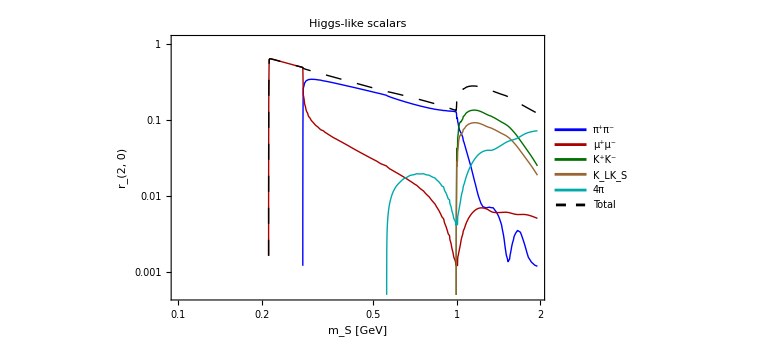

C:\Users\miksi\Dropbox\Science 2\Cosmology\Secondaries thermalization\plots\Higgs-like-scalars-r2-0.pdf

```mathematica
ptr20=LogLogPlot[Evaluate[Join[Table[EnergyFractionsToν[LLPsel,channel,mS],{channel,channelsS}],{EnergyFractionsToν[LLPsel,"Total",mS]}]],{mS,0.1,1.95},PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Brown},{Thick,Darker@Cyan},{Thick,Black,Dashing[0.02]},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@Join[channelsS,{"Total"}],{0.22,0.5}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_S [GeV]" , "r_(2, 0)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.1,1.95},{0.5*10^-3.,1.1}},PlotLabel->Style[Row[{"Higgs-like scalars"}],18,Black]]
Export[FileNameJoin[{NotebookDirectory[],"plots/Higgs-like-scalars-r2-0.pdf"}],ptr20]
```

## Mass and lifetime grids

```mathematica
LLPsel="Scalar";
MassGrid[LLPsel]=Join[Table[Round[10^mS,0.001],{mS,Log10[0.296],Log10[0.99],(Log10[0.99]-Log10[0.296])/60}],Table[x,{x,0.211,0.295,0.001}],Table[m,{m,0.01,0.21,0.01}],{0.995,1.,1.005,1.01,1.015,1.016,1.018,1.02,1.022,1.025,1.03,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.}]//Sort//N;
lifetimeGrid[LLPsel]=Join[Join[Table[i*0.01,{i,1,10}],Table[i*0.04,{i,3,20}],Table[10.^i,{i,Log10[1.2],Log10[20.],(Log10[20.]-Log10[1.2])/40}]],{0.012,0.016,0.025}]//Sort//DeleteDuplicates//N;
{mMaxCluster[LLPsel],τMaxCluster[LLPsel]}={0.7,10.};
```

## HNLs

## Name, description

```mathematica
(*Lifetimes and abundances*)
LLPsel="HNL-mixing-mu";
modelDescription[LLPsel]="HNLs coupled to muon neutrinos. See Ref. 1805.08567 for the description of the phenomenology. The tool SensCalc has been used for producing the fractions of neutrinos/pions/muons per decay.";
NamesLabel[LLPsel]="HNLs, mixing with ν_μ";
IfDecayOnly[LLPsel]=False;
```

## Abundance

```mathematica
(*Abundance as a function of mass and lifetime*)
YN[mN_,τ_]=Interpolation[DeleteDuplicatesBy[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNLs/HNL-abundances.mx"}],"MX"][[All,{1,2,4}]],{#[[1]],#[[2]]}&],InterpolationOrder->1][mN,τ];
nLLPini[LLPsel,mN_,τ_]=YN[mN,τ]*sUniverse[10.75,T](*(sIn/.Solve[sIn==sUniverse[10.75,T]+YS[mS,τ]*mX*sIn/T,sIn][[1]])*)/.{T->TiniEM};
```

## Phenomenology

```mathematica
(*Lifetime*)
τHNLdata=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNLs/HNLdecayWidth.dat"}],"Table"];
τLLP[LLPsel,mN_,U2_]=1/U2 Interpolation[{#[[1]],6.58*10^-25(#[[3]])^-1}&/@τHNLdata,InterpolationOrder->1][mN];
(*_______________________________________*)
(*Branching ratios*)
(*_______________________________________*)
(*dataHNLstemp=Import[FileNameJoin[{NotebookDirectory[],"HNL-decay-data.mx"}],"MX"];//AbsoluteTiming
len=8;
pdgid=6;
eid=4;
mid=5;
SetAttributes[ruleOwn,HoldAll];
ruleOwn[list_]:=Flatten[OwnValues/@(Unevaluated@list)]
νelist={12.,-12.};
νμlist={14.,-14.};
ντlist={16.,-16.};
πlist={211.,-211.};
μlist={13.,-13.};
Kchargedlist={321.,-321.};
KLlist={130.};
fractionToνTabulatedComp=Hold@Compile[{{mN,_Real},{νfraction,_Real},{data,_Real,1},{nprod,_Integer}},Module[{en=0.,pdg=0.,NKcharged=0.,Nμ=0.,Nπcharged=0.,NKL =0.,νefraction=0.,νμfraction=0.,ντfraction=0.},
Do[
en=Compile`GetElement[data,len*(j-1)+eid];
pdg=Compile`GetElement[data,len*(j-1)+pdgid];
If[pdg==-999.,Break[]];
If[MemberQ[νelist,pdg],νefraction+=en/mN];
If[MemberQ[νμlist,pdg],νμfraction+=en/mN];
If[MemberQ[ντlist,pdg],ντfraction+=en/mN];
If[MemberQ[πlist,pdg],Nπcharged+=1.];
If[MemberQ[Kchargedlist,pdg],NKcharged+=1.];
If[MemberQ[KLlist,pdg],NKcharged+=1.];
If[MemberQ[μlist,pdg],Nμ+=1.];
,{j,1,nprod,1}];
{νfraction/(3*mN)+(1-νfraction/mN)νefraction,νfraction/(3*mN)+(1-νfraction/mN)νμfraction,νfraction/(3*mN)+(1-νfraction/mN)ντfraction,Nμ,Nπcharged,NKcharged,NKL}
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]/.ruleOwn[{len,pdgid,eid,mid,νelist,νμlist,ντlist,πlist,Kchargedlist,KLlist,μlist}]//ReleaseHold
TempData=Join[dataHNLstemp[[All,{1}]],ParallelTable[Mean[fractionToνTabulatedComp[dataHNLstemp[[iv]][[1]],dataHNLstemp[[iv]][[2]][[1]],dataHNLstemp[[iv]][[2]][[2]],1/len Length[dataHNLstemp[[iv]][[2]][[2]][[1]]]]],{iv,1,Length[dataHNLstemp],1}],2]//Developer`ToPackedArray;//AbsoluteTiming
Export[FileNameJoin[{NotebookDirectory[],"phenomenology/HNLs/HNLdecayInfo.mx"}],TempData,"MX"];*)
TempData=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/HNLs/HNLdecayInfo.mx"}],"MX"];
{ξtoν[LLPsel,"ν_e",mN_],ξtoν[LLPsel,"ν_μ",mN_],ξtoν[LLPsel,"ν_τ",mN_]}=Interpolation[TempData[[All,{1,#}]],InterpolationOrder->1][mN]&/@{2,3,4};
NtoY[LLPsel,"μ^+",mN_]=NtoY[LLPsel,"μ^-",mN_]=1/2 Interpolation[TempData[[All,{1,5}]],InterpolationOrder->1][mN];
NtoY[LLPsel,"π^+",mN_]=NtoY[LLPsel,"π^-",mN_]=1/2 Interpolation[TempData[[All,{1,6}]],InterpolationOrder->1][mN];
NtoY[LLPsel,"K^+",mN_]=NtoY[LLPsel,"K^-",mN_]=1/2 Interpolation[TempData[[All,{1,7}]],InterpolationOrder->1][mN];
NtoY[LLPsel,"K_L",mN_]=Interpolation[TempData[[All,{1,8}]],InterpolationOrder->1][mN];
EKLkin[LLPsel,mS_]=0.;
EnergyFractionsToν[LLPsel,"Total",mN_]=Total[{ξtoν[LLPsel,"ν_e",mN],ξtoν[LLPsel,"ν_μ",mN],ξtoν[LLPsel,"ν_τ",mN]}]+1/mN Sum[energyToNeutrinoTotal[X]*NtoY[LLPsel,X,mN],{X,Yparticleslist}];
```

### Some plots

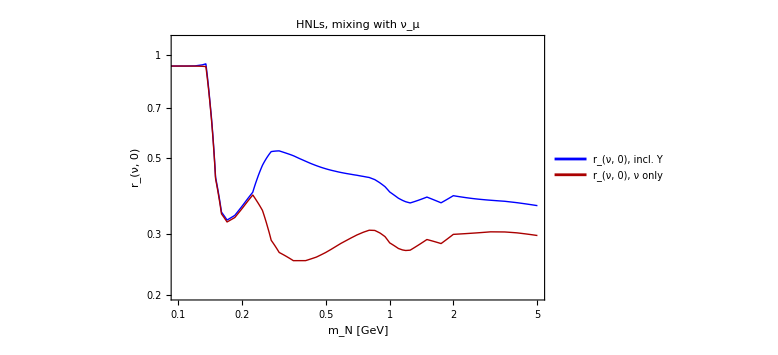
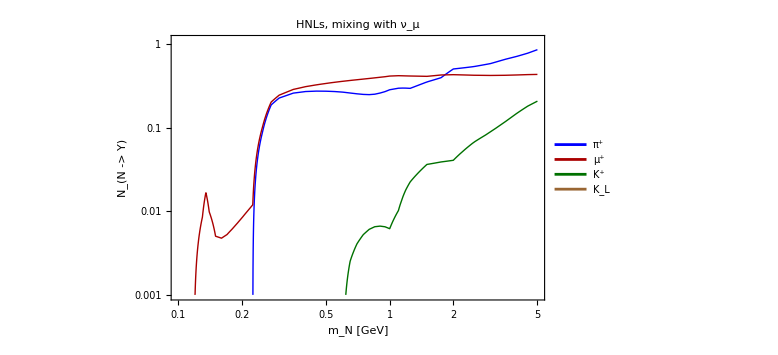

C:\Users\miksi\Dropbox\Science 2\Cosmology\Secondaries thermalization\plots\HNL-mixing-mu\HNL-mixing-mu-r2-0.pdf

C:\Users\miksi\Dropbox\Science 2\Cosmology\Secondaries thermalization\plots\HNL-mixing-mu\HNL-fractions.pdf

```mathematica
ptr20=LogLogPlot[Evaluate[{EnergyFractionsToν[LLPsel,"Total",mN],Total[{ξtoν[LLPsel,"ν_e",mN],ξtoν[LLPsel,"ν_μ",mN],ξtoν[LLPsel,"ν_τ",mN]}]}],{mN,0.02,5},FrameStyle->Directive[Thick,Black,18],PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Brown},{Thick,Darker@Cyan},{Thick,Black,Dashing[0.02]},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@Join[{"r_(ν, 0), incl. Y","r_(ν, 0), ν only"}],{0.85,0.85}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_N [GeV]" , "r_(ν, 0)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.1,5.},{0.2,1.1}},PlotLabel->Style[Row[{"HNLs, mixing with ν_μ"}],18,Black]];
ptr21=LogLogPlot[Evaluate[Table[NtoY[LLPsel,Y,mN],{Y,{"π^+","μ^+","K^+","K_L"}}]],{mN,0.02,5},FrameStyle->Directive[Thick,Black,18],PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Brown},{Thick,Darker@Cyan},{Thick,Black,Dashing[0.02]},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@Join[{"π^+","μ^+","K^+","K_L"}],{0.9,0.2}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_N [GeV]" , "N_(N -> Y)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.1,5.},{0.001,1.1}},PlotLabel->Style[Row[{"HNLs, mixing with ν_μ"}],18,Black]];
Style[Row[{ptr20,ptr21}],ImageSizeMultipliers->{1,1}]
Export[FileNameJoin[{NotebookDirectory[],"plots/"<>LLPsel<>"/"<>LLPsel<>"-r2-0.pdf"}],ptr20]
Export[FileNameJoin[{NotebookDirectory[],"plots/"<>LLPsel<>"/HNL-fractions.pdf"}],ptr21]
```

## Mass and lifetime grids

```mathematica
LLPsel="HNL-mixing-mu";
MassGrid[LLPsel]=Join[{0.05,0.06,0.07,0.09,0.1,0.104,0.11,0.12,0.13,0.135,0.14,0.15,0.16,0.17,0.19,0.2,0.204,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.31,0.33,0.35,0.37,0.39},Table[mN,{mN,0.41,1.01,0.03}]]//Sort//N;
lifetimeGrid[LLPsel]=Join[Join[Table[i*0.01,{i,1,10}],Table[i*0.04,{i,3,20}],Table[10.^i,{i,Log10[1.2],Log10[20.],(Log10[20.]-Log10[1.2])/40}]],{0.012,0.016,0.025}]//Sort//DeleteDuplicates//N;
{mMaxCluster[LLPsel],τMaxCluster[LLPsel]}={1.,10.};
```

## Toy particles decaying into pions

## Name, description

```mathematica
(*Lifetime and abundances*)
LLPsel="Toy-pions";
modelDescription[LLPsel]="A toy particle decaying solely into a pair of charged pions. The initial number density is fixed to be 0.002×s(T_ini)";
NamesLabel[LLPsel]="LLP decaying into pions";
IfDecayOnly[LLPsel]=False;
LLPsel="Toy-pions-decays-only";
modelDescription[LLPsel]="A toy particle decaying solely into a pair of charged pions, but where pions can only decay. The initial number density is fixed to be 0.002×s(T_ini)";
NamesLabel[LLPsel]="LLP decaying into pions (P_decay = 1)";
IfDecayOnly[LLPsel]=True;
modelsToyPions={"Toy-pions","Toy-pions-decays-only"};
```

## Abundance

```mathematica
Do[
(*LLP abundance as a function of mass and lifetime*)
YLLP[LLPsel,mS_,τ_]=If[mS<2*0.14,0.,2*10^-3.];
nLLPini[LLPsel,mS_,τ_]=YLLP[LLPsel,mS,τ]*sUniverse[10.75,T](*(sIn/.Solve[sIn==sUniverse[10.75,T]+YS[mS,τ]*mX*sIn/T,sIn][[1]])*)/.{T->TiniEM};
,{LLPsel,modelsToyPions}]
```

## Phenomenology

```mathematica
Do[
(*Numbers of Y particles produced per decay of the LLP*)
NtoY[LLPsel,"μ^+",mS_]=NtoY[LLPsel,"μ^-",mS_]=0.;
NtoY[LLPsel,"π^+",mS_]=NtoY[LLPsel,"π^-",mS_]=If[mS>2*0.14,1.,0.];
NtoY[LLPsel,"K^+",mS_]=NtoY[LLPsel,"K^-",mS_]=NtoY[LLPsel,"K_L",mS_]=0.;
EnergyFractionsToν[LLPsel,"Total",mS_]=NtoY[LLPsel,"π^+",mS]*1/mS(energyToNeutrinoTotal["π^+"]+energyToNeutrinoTotal["π^-"]);
nLLPini[LLPsel,mS_,τ_]=YLLP[mS,τ]*sUniverse[10.75,T](*(sIn/.Solve[sIn==sUniverse[10.75,T]+YS[mS,τ]*mX*sIn/T,sIn][[1]])*)/.{T->TiniEM};

(*Direct injections into neutrinos*)
{ξtoν[LLPsel,"ν_e",mS_],ξtoν[LLPsel,"ν_μ",mS_],ξtoν[LLPsel,"ν_τ",mS_]}={0.,0.,0.};
,{LLPsel,modelsToyPions}]
```

### Plots

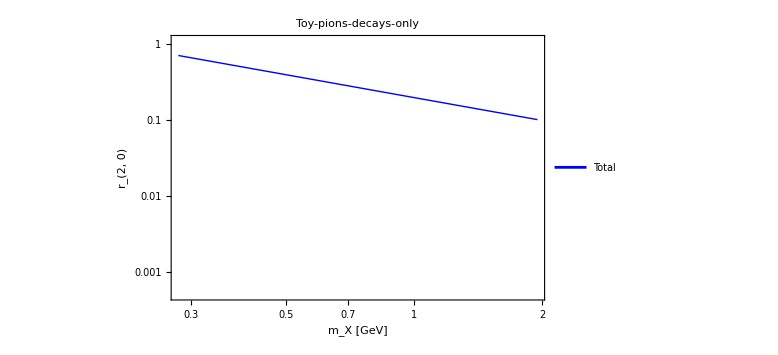

C:\Users\miksi\Dropbox\Science 2\Cosmology\Secondaries thermalization\plots\Toy-pions-decays-only-r2-0.pdf

```mathematica
ptr20=LogLogPlot[Evaluate[{EnergyFractionsToν[LLPsel,"Total",mS]}],{mS,0.28,1.95},PlotStyle->{{Thick,Blue}},PlotLegends->Placed[Style[#,20]&/@Join[{"Total"}],{0.13,0.7}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_X [GeV]" , "r_(2, 0)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.28,1.95},{0.5*10^-3.,1.1}},PlotLabel->Style[Row[{LLPsel}],18,Black]]
Export[FileNameJoin[{NotebookDirectory[],"plots/"<>LLPsel<>"-r2-0.pdf"}],ptr20]
(*The value of the scalar number density at the starting temperature TiniEM*)
```

## Mass and lifetime grids

```mathematica
Do[
MassGrid[LLPsel]=(*Join[Table[x,{x,0.14*2.01,1.,0.02}]]//Sort//N*){0.282,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.388,0.4,0.43,0.46,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.};
lifetimeGrid[LLPsel]=Join[Join[Table[i*0.01,{i,1,10}],Table[i*0.04,{i,3,20}],Table[10.^i,{i,Log10[1.2],Log10[20.],(Log10[20.]-Log10[1.2])/40}]],{0.012,0.016,0.025}]//Sort//DeleteDuplicates//N;
{mMaxCluster[LLPsel],τMaxCluster[LLPsel]}={1.,13.};
,{LLPsel,modelsToyPions}]
```

## Toy particles decaying into kaons

## Name, description

```mathematica
LLPsel="Toy-kaons";
modelDescription[LLPsel]="A toy particle decaying solely into a pair of charged  kaons. The initial number density is fixed to be 0.01×s(T_ini)";
NamesLabel[LLPsel]="LLP decaying into kaons";
IfDecayOnly[LLPsel]=True;
```

## Abundance

```mathematica
Do[
YLLP[LLPsel,mS_,τ_]=If[mS<2*0.5,0.,10*10^-3.];
(*LLP abundance as a function of mass and lifetime*)
nLLPini[LLPsel,mS_,τ_]=YLLP[LLPsel,mS,τ]*sUniverse[10.75,T](*(sIn/.Solve[sIn==sUniverse[10.75,T]+YS[mS,τ]*mX*sIn/T,sIn][[1]])*)/.{T->TiniEM};
,{LLPsel,{"Toy-kaons"}}]
```

## Phenomenology

```mathematica
Do[
(*Numbers of Y particles produced per decay of the LLP*)
NtoY[LLPsel,"μ^+",mS_]=NtoY[LLPsel,"μ^-",mS_]=0.;
NtoY[LLPsel,"π^+",mS_]=NtoY[LLPsel,"π^-",mS_]=0.;
NtoY[LLPsel,"K^+",mS_]=NtoY[LLPsel,"K^-",mS_]=If[mS>2*0.5,1.,0.];
NtoY[LLPsel,"K_L",mS_]=0.;
EKLkin[LLPsel,mS_]=0.;
EnergyFractionsToν[LLPsel,"Total",mS_]=NtoY[LLPsel,"K^+",mS]*1/mS(energyToNeutrinoTotal["K^+"]+energyToNeutrinoTotal["K^-"]);
(*Direct injections into neutrinos*)
{ξtoν[LLPsel,"ν_e",mS_],ξtoν[LLPsel,"ν_μ",mS_],ξtoν[LLPsel,"ν_τ",mS_]}={0.,0.,0.};
,{LLPsel,{"Toy-kaons"}}]
(*The value of the scalar number density at the starting temperature TiniEM*)
```

### Plots

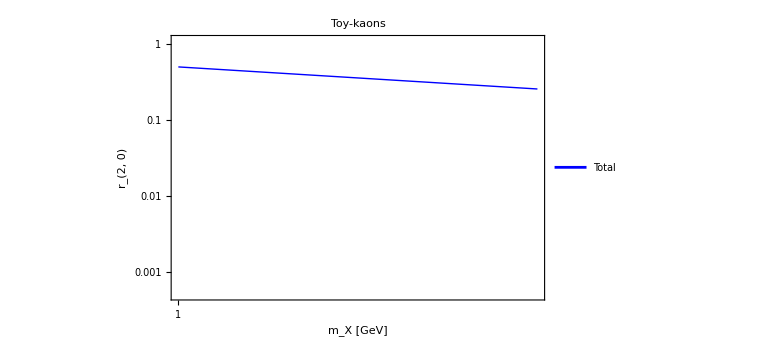

C:\Users\miksi\Dropbox\Science 2\Cosmology\Secondaries thermalization\plots\Toy-kaons-r2-0.pdf

```mathematica
ptr20=LogLogPlot[Evaluate[{EnergyFractionsToν[LLPsel,"Total",mS]}],{mS,1.,1.95},PlotStyle->{{Thick,Blue}},PlotLegends->Placed[Style[#,20]&/@Join[{"Total"}],{0.13,0.7}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_X [GeV]" , "r_(2, 0)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.,1.95},{0.5*10^-3.,1.1}},PlotLabel->Style[Row[{LLPsel}],18,Black]]
Export[FileNameJoin[{NotebookDirectory[],"plots/"<>LLPsel<>"-r2-0.pdf"}],ptr20]
```

## Mass and lifetime grids

```mathematica
LLPsel="Toy-kaons";
MassGrid[LLPsel]=(*Join[Table[x,{x,0.14*2.01,1.,0.02}]]//Sort//N*){0.282,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.388,0.4,0.43,0.46,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.};
lifetimeGrid[LLPsel]=Join[Join[Table[i*0.01,{i,1,10}],Table[i*0.04,{i,3,20}],Table[10.^i,{i,Log10[1.2],Log10[20.],(Log10[20.]-Log10[1.2])/40}]],{0.012,0.016,0.025}]//Sort//DeleteDuplicates//N;
{mMaxCluster[LLPsel],τMaxCluster[LLPsel]}={1.,13.};
```

# Simple studies

## Simple estimates

```mathematica
tmin=tTMeVradiationDominated[9]
nXint[t_,τ_,χSuppression_,g_]=Exp[-(t-tmin)/τ]*g*χSuppression*Integrate[(4Pi)/(2Pi)^3 p^2/(Exp[p/T]-1),{p,0,Infinity},Assumptions->T>0]/.{T->TtRadiationDominated[t]};
ΓdecΓann[particle_,T_,τX_,ξ_,g_]:=(1/lifetime[particle]^2)/(nXint[tTMeVradiationDominated[T],τX,ξ,g]/τX*σvAnnTot[particle,10^-3 T]/GeVtosm1)
ΓdecΓpn[particle_,T_,τX_,ξ_,g_]:=(1/lifetime[particle])/(nBSBBN[10^-3 T]/2*(σvNuclTot[particle,"p",10^-3 T]/GeVtosm1+σvNuclTot[particle,"n",10^-3 T]/GeVtosm1))
Join[{{"particle","ϵ_ann","ϵ_nucl"}},Table[{particle,ΓdecΓann[particle,3.,0.05,0.1,1],If[MemberQ[{"μ^-","μ^-","K^+"},particle],"inf",ΓdecΓpn[particle,3.,0.05,0.1,1]]},{particle,{"μ^-","π^-","K^-","K^+","K_L","K_S"}}]]
```

### Cross-checks

Kaon-driven and pion-driven interactions with nucleons do not violate electric charge conservation

```mathematica
Print["Electric charge dynamics related to kaons - their disappearance and increasing population of pions: X_1 = -∑_K Q_K(dn_K/dt)_(K - nucleon) - ∑_π Q_π(dn_π/dt)_(K  - nucleon)"]
expr1=-charge["K^-"]*dndt["K^-","Nucleon"][[2]]-charge["K_L"]*dndt["K_L","Nucleon"][[2]]-(charge["π^+"]*Sum[SourceTerms[K,"π^+","Nucleon",nB,T][[2]],{K,{"K^-","K_L"}}]+charge["π^-"]*Sum[SourceTerms[K,"π^-","Nucleon",nB,T][[2]],{K,{"K^-","K_L"}}])//Expand
Print["Electric charge dynamics related to p<->n conversion in presence of pions: X_2 = -∑_π Q_π(dn_π/dt)_(π - nucleon)"]
expr2=-charge["π^-"]*dndt["π^-","Nucleon"][[2]]-charge["π^+"]*dndt["π^+","Nucleon"][[2]]//Expand
Print["Dynamics of protons: X_3 = Q_pdn_p/dt"]
expr3=nB*dndt["X_n","All"][[2]]/.{BrToKCharged->1,BrToKLong->1,IfPionConversion->True}//Expand
Print["If X_1+X_2 == X_3"]
expr1+expr2==-expr3
```

Electric charge dynamics related to kaons - their disappearance and increasing population of pions: X_1 = -∑_K Q_K(dn_K/dt)_(K - nucleon) - ∑_π Q_π(dn_π/dt)_(K  - nucleon)

-1. If[IfConversion,4.55927×10^25 nB nKL(t) (1-1.×10^15 Xn(t))+1.8997×10^40 nB nKL(t) Xn(t),0.]+1. If[IfConversion,1.8997×10^25 nB nKL(t) (1-1.×10^15 Xn(t))+4.55927×10^40 nB nKL(t) Xn(t),0.]-1. If[IfConversion,(1.79991×10^24 nB nKminus(t) (1-1.×10^15 Xn(t)))/((1-ⅇ^(-0.01869/(√T))) √T)+0.,0.]+1. If[IfConversion,(2.81415×10^24 nB nKminus(t) (1-1.×10^15 Xn(t)))/((1-ⅇ^(-0.01869/(√T))) √T)+3.25532×10^41 nB nKminus(t) Xn(t),0.]+(3.19548×10^39 nB nKminus(t) Xn(t))/((1-ⅇ^(-0.01869/(√T))) √T)-(3.19548×10^24 nB nKminus(t))/((1-ⅇ^(-0.01869/(√T))) √T)-2.27964×10^41 nB nKminus(t) Xn(t)

Electric charge dynamics related to p<->n conversion in presence of pions: X_2 = -∑_π Q_π(dn_π/dt)_(π - nucleon)

(6.72347×10^37 nB nπminus(t) Xn(t))/((1-ⅇ^(-0.0123462/(√T))) √T)-(6.72347×10^22 nB nπminus(t))/((1-ⅇ^(-0.0123462/(√T))) √T)+5.99037×10^39 nB nπplus(t) Xn(t)

Dynamics of protons: X_3 = Q_pdn_p/dt

All nB

If X_1+X_2 == X_3

-1. If[IfConversion,4.55927×10^25 nB nKL(t) (1-1.×10^15 Xn(t))+1.8997×10^40 nB nKL(t) Xn(t),0.]+1. If[IfConversion,1.8997×10^25 nB nKL(t) (1-1.×10^15 Xn(t))+4.55927×10^40 nB nKL(t) Xn(t),0.]-1. If[IfConversion,(1.79991×10^24 nB nKminus(t) (1-1.×10^15 Xn(t)))/((1-ⅇ^(-0.01869/(√T))) √T)+0.,0.]+1. If[IfConversion,(2.81415×10^24 nB nKminus(t) (1-1.×10^15 Xn(t)))/((1-ⅇ^(-0.01869/(√T))) √T)+3.25532×10^41 nB nKminus(t) Xn(t),0.]+(3.19548×10^39 nB nKminus(t) Xn(t))/((1-ⅇ^(-0.01869/(√T))) √T)-(3.19548×10^24 nB nKminus(t))/((1-ⅇ^(-0.01869/(√T))) √T)-2.27964×10^41 nB nKminus(t) Xn(t)+(6.72347×10^37 nB nπminus(t) Xn(t))/((1-ⅇ^(-0.0123462/(√T))) √T)-(6.72347×10^22 nB nπminus(t))/((1-ⅇ^(-0.0123462/(√T))) √T)+5.99037×10^39 nB nπplus(t) Xn(t)==-All nB

## Instant equilibrium

## Muon-antimuon population

```mathematica
(*Annihilation cross-section in the units of GeV*)
σvAnn["μ"]=(σvAnn["μ^+","e^+"]+σvAnn["μ^+","γ"])/.{mμ->0.105,αEM->1/137.}
(*Toy system of equations for μ and μ̄. The first term: decays. The second term: annihilations. The third term: source*)
solμ[τ_,χSuppression_,g_]:=NDSolve[Rationalize[{nμ'[t]+3*Hval[t]*nμ[t]==-nμ[t]/lifetime["μ^+"]+nXint[t,τ,χSuppression,g]/τ-nμ[t]*nμbar[t]*σvAnnTot["μ^+",TtRadiationDominated[t]]/GeVtosm1,nμbar'[t]+3*Hval[t]*nμbar[t]==-nμbar[t]/lifetime["μ^-"]+nXint[t,τ,χSuppression,g]/τ-nμ[t]*nμbar[t]*σvAnnTot["μ^-",TtRadiationDominated[t]]/GeVtosm1,nμ[tmin]==0,nμbar[tmin]==0},0],{nμ[t],nμbar[t]},{t,tmin,200*τ},WorkingPrecision->40][[1]]
solμdynEq[t_,τ_,χSuppression_,g_]=With[{nμbarsol=(nμbar[t]/.Solve[-nμbar[t]/lifetime["μ^+"]+nXint[t,τ,χSuppression,g]/τ-nμ[t]*nμbar[t]*σvAnnTot["μ^+",TtRadiationDominated[t]]/GeVtosm1==0,nμbar[t]][[1]])},nμ[t]/.Solve[-nμ[t]/lifetime["μ^-"]+nXint[t,τ,χSuppression,g]/τ-nμ[t]*nμbarsol*σvAnnTot["μ^-",TtRadiationDominated[t]]/GeVtosm1==0,nμ[t]][[2]]];
(*Toy system of equations for μ and μ̄. The same as previous but without decays*)
solμNoAnn[τ_,χSuppression_,g_]:=NDSolve[Rationalize[{nμ'[t]+3*Hval[t]*nμ[t]==-nμ[t]/τμ+nXint[t,τ,χSuppression,g]/τ,nμbar'[t]+3*Hval[t]*nμbar[t]==-nμbar[t]/τμ+nXint[t,τ,χSuppression,g]/τ,nμ[tmin]==0,nμbar[tmin]==0},0],{nμ[t],nμbar[t]},{t,tmin,200*τ},WorkingPrecision->40][[1]]
nμtest[t_]=Quiet[nμ[t]/.solμ[0.03,1,1]];
nμNoAnntest[t_]=Quiet[nμ[t]/.solμNoAnn[0.03,1,1]];
LogLogPlot[{nμtest[t]/nμNoAnntest[t],1},{t,1.001tmin,0.2},ImageSize->Large,Frame->True]
nμtest2[t_]=Quiet[nμ[t]/.solμ[0.03,1/8*1/3,4]];
nμNoAnntest2[t_]=Quiet[nμ[t]/.solμNoAnn[0.03,1/8*1/3,4]];
LogLogPlot[{nμtest2[t]/nμNoAnntest2[t],1},{t,1.001tmin,0.2},ImageSize->Large,Frame->True]
```

### Plots

```mathematica
tsol001[τ_]=t/.Solve[Exp[-t/τ]==0.01,t][[1]]
PlotProduction[nμtest2_,τtest_,ξtest_,gtest_]:=Module[{τ,ξ,g},
BrμDec[T_]=(1/lifetime["μ^+"])/(1/lifetime["μ^+"]+nμtest2[tTMeVradiationDominated[T]] σvAnnTot["μ^+",T]/GeVtosm1);
BrμAnn[T_]=(nμtest2[tTMeVradiationDominated[T]] σvAnnTot["μ^+",T]/GeVtosm1)/(1/lifetime["μ^+"]+nμtest2[tTMeVradiationDominated[T]] σvAnnTot["μ^+",T]/GeVtosm1);
lineStyle={Thick,Gray,Dashed};

line1=Line[{{10^3 TtRadiationDominated[tsol001[τtest]],-10.},{10^3 TtRadiationDominated[tsol001[τtest]],5}}];
fractionPionPlot=LogPlot[Evaluate[{BrμDec[T],BrμAnn[T]}],{T,1,5},PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Blue},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},Epilog->{Directive[lineStyle],line1},PlotLegends->Placed[Style[#,20]&/@{"Decay","Annihilation"},{0.8,0.2}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"T [MeV]" , "Fraction of muons"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1,5},{10^-3.,1.3}},PlotLabel->Style[Row[{"τ = ",τtest," s, ξ = ",N[ξtest],", g = ",gtest}],18,Black]]
]
ξtest=1/24;
τtest=0.03;
gtest=4;
nμtest2[t_]=Quiet[nμ[t]/.solμ[τtest,ξtest,gtest]];
pt1=PlotProduction[nμtest2,τtest,ξtest,gtest];
ξtest=1/24;
τtest=0.1;
gtest=4;
nμtest2[t_]=Quiet[nμ[t]/.solμ[τtest,ξtest,gtest]];
pt2=PlotProduction[nμtest2,τtest,ξtest,gtest];
Style[Row[{pt1,pt2}],ImageSizeMultipliers->{1, 1}]
Export[FileNameJoin[{NotebookDirectory[],"plots/Secondary particles/fractionMuon.pdf"}],pt1];
Export[FileNameJoin[{NotebookDirectory[],"plots/Secondary particles/fractionMuon2.pdf"}],pt2];
```

Cumulative numbers of muons

```mathematica
CumulativeNumberμDecExact[τtest_,ξtest_,gtest_]:=Block[{},
nμsol[t_]:=Quiet[nμ[t]/.solμ[τtest,ξtest,gtest]];
nμsol1[t_]=nμsol[t];
{NIntegrate[nμsol1[t]/lifetime["μ^+"](t/tmin)^(3/2),{t,tmin,100*τtest}]/NIntegrate[nXint[t,τtest,ξtest,gtest]/τtest(t/tmin)^(3/2),{t,tmin,100*τtest}],NIntegrate[solμdynEq[t,τtest,ξtest,gtest]/lifetime["μ^+"](t/tmin)^(3/2),{t,tmin,100*τtest}]/NIntegrate[nXint[t,τtest,ξtest,gtest]/τtest(t/tmin)^(3/2),{t,tmin,100*τtest}]}
]
CumulativeNumberμDecEquilibrium[τtest_,ξtest_,gtest_]:=Block[{},
{NIntegrate[solμdynEq[t,τtest,ξtest,gtest]/lifetime["μ^+"](t/tmin)^(3/2),{t,tmin,100*τtest}]/NIntegrate[nXint[t,τtest,ξtest,gtest]/τtest(t/tmin)^(3/2),{t,tmin,100*τtest}],NIntegrate[solμdynEq[t,τtest,ξtest,gtest]^2 σvAnnTot["μ^+",T]/GeVtosm1(t/tmin)^(3/2),{t,tmin,100*τtest}]/NIntegrate[nXint[t,τtest,ξtest,gtest]/τtest(t/tmin)^(3/2),{t,tmin,100*τtest}]}
]
tabFractionDecayedμ1=ParallelTable[{τ,CumulativeNumberμDecEquilibrium[τ,1/24,4][[1]]},{τ,0.02,1.,0.01}];
tabFractionDecayedμ2=ParallelTable[{τ,CumulativeNumberμDecEquilibrium[τ,1/240,4][[1]]},{τ,0.02,1.,0.01}];
pt1=ListLogLogPlot[Evaluate[{tabFractionDecayedμ1,tabFractionDecayedμ2}],Joined->True,PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Blue},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@{"ξ = 1/24, g = 4","ξ = 1/240, g = 4"},{0.8,0.2}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"τ_X [s]" , "(χ^μ)_dec"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.02,1},{10^-3.,1.3}}(*,PlotLabel->Style[Row[{"τ = ",τtest," s, ξ = ",N[ξtest],", g = ",gtest}],18,Black]*)]
Export[FileNameJoin[{NotebookDirectory[],"plots/Secondary particles/muonComovingDecayFraction.pdf"}],pt1]
```

## Pion-antipion population

```mathematica
σvAnn["π",t_]=σvAnn["π^+","π^0",TtRadiationDominated[t]];
(*Toy system of equations for π^+ and π^-. The first term: decays. The second term: annihilations. The third term: source*)
solπ[τ_,χSuppression_,g_]:=NDSolve[Rationalize[{nπ'[t]+3*Hval[t]*nπ[t]==-nπ[t]/lifetime["π^+"]+nXint[t,τ,χSuppression,g]/τ-nπ[t]*nπbar[t]*σvAnnTot["π^-",TtRadiationDominated[t]]/GeVtosm1-nπ[t]*npπ[TtRadiationDominated[t]]*σvConv["π^-","p->n",TtRadiationDominated[t]]/GeVtosm1,nπbar'[t]+3*Hval[t]*nπbar[t]==-nπbar[t]/lifetime["π^+"]+nXint[t,τ,χSuppression,g]/τ-nπ[t]*nπbar[t]*σvAnnTot["π^+",TtRadiationDominated[t]]/GeVtosm1-nπbar[t]*nnπ[TtRadiationDominated[t]]*σvConv["π^+","n->p",TtRadiationDominated[t]]/GeVtosm1,nπ[tmin]==0,nπbar[tmin]==0},0],{nπ[t],nπbar[t]},{t,tmin,100*τ},WorkingPrecision->45][[1]]
solπNoAnn[τ_,χSuppression_,g_]:=NDSolve[Rationalize[{nπ'[t]+3*Hval[t]*nπ[t]==-nπ[t]/lifetime["π^+"]+nXint[t,τ,χSuppression,g]/τ,nπbar'[t]+3*Hval[t]*nπbar[t]==-nπbar[t]/lifetime["π^-"]+nXint[t,τ,χSuppression,g]/τ,nπ[tmin]==0,nπbar[tmin]==0},0],{nπ[t],nπbar[t]},{t,tmin,100*τ},WorkingPrecision->45][[1]]
nπtest[t_]=Quiet[nπ[t]/.solπ[0.03,1,1]];
nπNoAnntest[t_]=Quiet[nπ[t]/.solπNoAnn[0.03,1,1]];
LogLogPlot[{nπtest[t]/nπNoAnntest[t],1},{t,1.001tmin,0.2},ImageSize->Large,Frame->True]
nπtest2[t_]=Quiet[nπ[t]/.solπ[0.03,1/8*1/3,4]];
nπNoAnntest2[t_]=Quiet[nπ[t]/.solπNoAnn[0.03,1/8*1/3,4]];
LogLogPlot[{nπtest2[t]/nπNoAnntest2[t],1},{t,1.001tmin,0.3},ImageSize->Large,Frame->True]
```

### Dynamic equilibrium solution and cumulative fractions

```mathematica
solπdynEq[t_,τ_,χSuppression_,g_]=nπ[t]/.Solve[-nπ[t]/lifetime["π^+"]+nXint[t,τ,χSuppression,g]/τ-nπ[t]^2 σvAnnTot["π^+",TtRadiationDominated[t]]/GeVtosm1-nπ[t]*npπ[TtRadiationDominated[t]]*σvConv["π^+","p->n",TtRadiationDominated[t]]/GeVtosm1==0,nπ[t]][[2]];
solπdynEqInt[τ_,χSuppression_,g_]:=Block[{},
solexact[t_]=solπdynEq[t,τ,χSuppression,g];
tlist=DeleteDuplicates[Join[Table[10^t,{t,Log10[tmin],Log10[tmin+(100τtest-tmin)/100],(Log10[tmin+(100τtest-tmin)/100]-Log10[tmin])/10}],Table[t,{t,tmin+2(100τtest-tmin)/100,100τtest,(100τtest-tmin-2(100τtest-tmin)/100)/100}]]//N]//Sort;
Exp[Interpolation[Log[{#,solexact[#]}&/@tlist],InterpolationOrder->1][Log[t]]]
]
solπdynEqNoAnn[t_,τ_,χSuppression_,g_]=nπ[t]/.Solve[-nπ[t]/lifetime["π^-"]+nXint[t,τ,χSuppression,g]/τ-nπ[t]*npπ[TtRadiationDominated[t]]*σvConv["π^-","p->n",TtRadiationDominated[t]]/GeVtosm1==0,nπ[t]][[1]]//Simplify;
CumulativeNumberπDecEquilibrium[τtest_,ξtest_,gtest_]:=Block[{},
soldyn[t_]=solπdynEq[t,τtest,ξtest,gtest];
{τtest,NIntegrate[soldyn[t]/lifetime["π^-"](t/tmin)^(3/2),{t,tmin,100*τtest},Method->"InterpolationPointsSubdivision"]/NIntegrate[nXint[t,τtest,ξtest,gtest]/τtest(t/tmin)^(3/2),{t,tmin,100*τtest}],NIntegrate[soldyn[t]^2 σvAnnTot["π^+",TtRadiationDominated[t]]/GeVtosm1(t/tmin)^(3/2),{t,tmin,100*τtest},Method->"InterpolationPointsSubdivision"]/NIntegrate[nXint[t,τtest,ξtest,gtest]/τtest(t/tmin)^(3/2),{t,tmin,100*τtest}],NIntegrate[soldyn[t]*nnπ[TtRadiationDominated[t]]*σvConv["π^+","n->p",TtRadiationDominated[t]]/GeVtosm1(t/tmin)^(3/2),{t,tmin,100*τtest},Method->"InterpolationPointsSubdivision"]/NIntegrate[nXint[t,τtest,ξtest,gtest]/τtest(t/tmin)^(3/2),{t,tmin,100*τtest}]}
]
CumulativeNumberπDecEquilibrium1[0.1,0.1,4]//AbsoluteTiming
CumulativeNumberπDecEquilibriumNoAnn[τtest_,ξtest_,gtest_]:=Block[{},
soldyn[t_]=solπdynEqNoAnn[t,τtest,ξtest,gtest];
{τtest,NIntegrate[soldyn[t]/lifetime["π^+"](t/tmin)^(3/2),{t,tmin,100*τtest}]/NIntegrate[nXint[t,τtest,ξtest,gtest]/τtest(t/tmin)^(3/2),{t,tmin,100*τtest}],NIntegrate[soldyn[t]*nnπ[TtRadiationDominated[t]]*σvConv["π^+","n->p",TtRadiationDominated[t]]/GeVtosm1(t/tmin)^(3/2),{t,tmin,100*τtest}]/NIntegrate[nXint[t,τtest,ξtest,gtest]/τtest(t/tmin)^(3/2),{t,tmin,100*τtest}]}
]
tabFractionDecayedπ1=ParallelTable[CumulativeNumberπDecEquilibrium[τ,1/24,4],{τ,0.02,1.,0.01}];
tabFractionDecayedπ2=ParallelTable[CumulativeNumberπDecEquilibrium[τ,1/240,4],{τ,0.02,1.,0.01}];
pt1=ListLogLogPlot[Evaluate[{tabFractionDecayedπ1[[All,{1,2}]],tabFractionDecayedπ2[[All,{1,2}]]}],Joined->True,PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green},{Thick,Blue},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@{"ξ = 1/24, g = 4","ξ = 1/240, g = 4"},{0.8,0.2}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"τ_X [s]" , "(χ^π)_dec"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{0.02,1},{10^-3.,1.3}}(*,PlotLabel->Style[Row[{"τ = ",τtest," s, ξ = ",N[ξtest],", g = ",gtest}],18,Black]*)]
Export[FileNameJoin[{NotebookDirectory[],"plots/Secondary particles/pionComovingDecayFraction.pdf"}],pt1]
```

### Plots

```mathematica
tsol001[τ_]=t/.Solve[Exp[-t/τ]==0.01,t][[1]]
PlotProduction[nπtest2_,τtest_,ξtest_,gtest_]:=Module[{τ,ξ,g},
BrπDec[T_]=(1/lifetime["π^+"])/(1/lifetime["π^+"]+nπtest2[tTMeVradiationDominated[T]] σvAnnTot["π^+",10^-3 T]/GeVtosm1+nnπ[10^-3 T]*σvConv["π^+","n->p",10^-3 T]/GeVtosm1);
BrπAnn[T_]=(nπtest2[tTMeVradiationDominated[T]] σvAnnTot["π^+",10^-3 T]/GeVtosm1)/(1/lifetime["π^+"]+nπtest2[tTMeVradiationDominated[T]] σvAnnTot["π^+",10^-3 T]/GeVtosm1+nnπ[10^-3 T]*σvConv["π^+","n->p",10^-3 T]/GeVtosm1);
BrπConv[T_]=(nnπ[10^-3 T]*σvConv["π^+","n->p",10^-3 T]/GeVtosm1)/(1/lifetime["π^+"]+nπtest2[tTMeVradiationDominated[T]] σvAnnTot["π^+",10^-3 T]/GeVtosm1+nnπ[10^-3 T]*σvConv["π^+","n->p",10^-3 T]/GeVtosm1);
lineStyle={Thick,Gray,Dashed};

line1=Line[{{10^3 TtRadiationDominated[tsol001[τtest]],-10.},{10^3 TtRadiationDominated[tsol001[τtest]],5}}];
fractionPionPlot=LogPlot[Evaluate[{BrπDec[T],BrπAnn[T],BrπConv[T]}],{T,1,5},PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Blue},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},Epilog->{Directive[lineStyle],line1},PlotLegends->Placed[Style[#,20]&/@{"Decay","Annihilation","p<->n"},{0.8,0.2}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"T [MeV]" , "Fraction of pions"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1,5},{10^-3.,1.3}},PlotLabel->Style[Row[{"τ = ",τtest," s, ξ = ",N[ξtest],", g = ",gtest}],18,Black]]
]
ξtest=1/24;
τtest=0.03;
gtest=4;
nπtest2[t_]=Quiet[nπ[t]/.solπ[τtest,ξtest,gtest]];
pt1=PlotProduction[nπtest2,τtest,ξtest,gtest];
ξtest=1/24;
τtest=0.1;
gtest=4;
nπtest2[t_]=Quiet[nπ[t]/.solπ[τtest,ξtest,gtest]];
pt2=PlotProduction[nπtest2,τtest,ξtest,gtest];
Style[Row[{pt1,pt2}],ImageSizeMultipliers->{1, 1}]
Export[FileNameJoin[{NotebookDirectory[],"plots/Secondary particles/fractionPion.pdf"}],pt1];
Export[FileNameJoin[{NotebookDirectory[],"plots/Secondary particles/fractionPion2.pdf"}],pt2];
```

```mathematica
nYbarsolDynEq=nYbar/.Solve[nX/τX-nYbar/τY-nY*nYbar*σvann==0,nYbar][[1]]
nYsolDynEq=nY/.Solve[nX/τX-nY/τY-nY*nYbarsolDynEq*σvann-nY*nB*(1/3 σvnucln+2/3 σvnuclp)==0,nY][[2]]//Simplify
nYbarsolDynEq=nYbarsolDynEq/.{nY->nYsolDynEq}//Simplify
```

```mathematica
ttest=0.02;
τXtest=0.1;
nYexample=nYsolDynEq/.{nX->nXint[ttest,τXtest,0.01,4],τX->τXtest,nB->nBSBBN[TtRadiationDominated[ttest]],τY->lifetime["K^+"],σvnucln->σvNuclTot["K^-","n",TtRadiationDominated[ttest]]/GeVtosm1,σvnuclp->σvNuclTot["K^-","p",TtRadiationDominated[ttest]]/GeVtosm1,σvann->σvAnnTot["K^-",TtRadiationDominated[ttest]]/GeVtosm1}
nYbarexample=nYbarsolDynEq/.{nX->nXint[ttest,τXtest,0.01,4],τX->τXtest,nB->nBSBBN[TtRadiationDominated[ttest]],τY->lifetime["K^+"],σvnucln->σvNuclTot["K^-","n",TtRadiationDominated[ttest]]/GeVtosm1,σvnuclp->σvNuclTot["K^-","p",TtRadiationDominated[ttest]]/GeVtosm1,σvann->σvAnnTot["K^-",TtRadiationDominated[ttest]]/GeVtosm1}
```

```mathematica
(nBSBBN[TtRadiationDominated[ttest]]*σvNuclTot["K^-","p",TtRadiationDominated[ttest]])/(nYbarexample*σvAnnTot["K^-",TtRadiationDominated[ttest]])
```

```mathematica
(nBSBBN[TtRadiationDominated[ttest]]*σvNuclTot["K^-","p",TtRadiationDominated[ttest]])/(nYexample*σvAnnTot["K^-",TtRadiationDominated[ttest]])
```

## Kaon-antikaon population

```mathematica
(*Toy system of equations for π^+ and π^-. The first term: decays. The second term: annihilations. The third term: source*)
sc=10^15;
solK[τ_,χSuppression_,g_]:=NDSolve[Rationalize[{sc*Xn'[t]==(1-sc*Xn[t])*(nKminus[t]*σvConv["K^-","p->n",TtRadiationDominated[t]]/GeVtosm1+nKLbar[t]*σvConv["(K̄)_L","p->n",TtRadiationDominated[t]]/GeVtosm1)-sc*Xn[t]*(nKminus[t]*σvConv["K^-","n->p",TtRadiationDominated[t]]/GeVtosm1+nKLbar[t]*σvConv["(K̄)_L","n->p",TtRadiationDominated[t]]/GeVtosm1),nKminus'[t]+3*Hval[t]*nKminus[t]==-nKminus[t]/lifetime["K^-"]+nXint[t,τ,χSuppression,g]/τ-nKminus[t]*nKplus[t]*σvAnnTot["K^-",TtRadiationDominated[t]]/GeVtosm1-nKminus[t]*nBSBBN[TtRadiationDominated[t]]*((1-sc*Xn[t])*σvConv["K^-","p->n",TtRadiationDominated[t]]/GeVtosm1+sc*Xn[t]*σvConv["K^-","n->p",TtRadiationDominated[t]]/GeVtosm1),nKplus'[t]+3*Hval[t]*nKplus[t]==-nKplus[t]/lifetime["K^+"]+nXint[t,τ,χSuppression,g]/τ-nKplus[t]*nKminus[t]*σvAnnTot["K^+",TtRadiationDominated[t]]/GeVtosm1,nKLbar'[t]+3*Hval[t]*nKLbar[t]==-nKLbar[t]/lifetime["(K̄)_L"]+nXint[t,τ,χSuppression,g]/τ-nKLbar[t]*nKL[t]*σvAnnTot["(K̄)_L",TtRadiationDominated[t]]/GeVtosm1-nKLbar[t]*nBSBBN[TtRadiationDominated[t]]*((1-sc*Xn[t])*σvConv["(K̄)_L","p->n",TtRadiationDominated[t]]/GeVtosm1+sc*Xn[t]*σvConv["(K̄)_L","n->p",TtRadiationDominated[t]]/GeVtosm1),nKL'[t]+3*Hval[t]*nKL[t]==-nKL[t]/lifetime["K_L"]+nXint[t,τ,χSuppression,g]/τ-nKL[t]*nKLbar[t]*σvAnnTot["K_L",TtRadiationDominated[t]]/GeVtosm1,nKminus[tmin]==0,nKplus[tmin]==0,nKL[tmin]==0,nKLbar[tmin]==0,Xn[tmin]==sc^-1/2},0],{nKplus[t],nKminus[t],nKL[t],nKLbar[t],Xn[t]},{t,tmin,100*τ},WorkingPrecision->45][[1]]
τXtest=0.3;
soltest=solK[τXtest,0.1,1];//AbsoluteTiming
{nKplustest[t_],nKminustest[t_],nKLtest[t_],nKLbartest[t_],Xntest[t_]}=Quiet[#[t]/.soltest]&/@{nKplus,nKminus,nKL,nKLbar,Xn};
Xntest[t_]=sc*Xntest[t];
LogLogPlot[Evaluate[{nKplustest[t]/nKminustest[t],nKLtest[t]/nKLbartest[t],1}],{t,1.001tmin,18*τXtest},PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Gray,Dashing[0.02]},{Thick,Darker@Darker@Green},{Thick,Blue},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@{"K^+/K^-","K_L/(K̄)_L"},{0.1,0.2}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"t [s]" , "n_Y/n_(Ȳ)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{tmin,18*τXtest},All},PlotLabel->Style[Row[{"ξ = 0.1, g = 1, τ = ",τXtest," s"}],18,Black]]
LogLogPlot[Evaluate[{nKplustest[t],nKminustest[t],nKLtest[t],nKLbartest[t]}],{t,1.001tmin,10*0.03}]
```

# Generating the evolution of Ys

```mathematica
(*Flatten[ResourceFunction["MonitorProgress"]@ParallelTable[mergedFunction["Model-independent-Kaons",mS,τ,False],{mS,{1.02,1.03,1.04,1.05,1.06,1.07}},{τ,{0.02,0.2,20.}}],1]//N;*)
```

## Definitions

```mathematica
Print["List of available models:"]
modellist=Keys[DownValues@NtoY][[All,1,1]]//DeleteDuplicates
descriptionlist=modelDescription[#]&/@modellist;
(*The routine converting the output for cluster*)
exportOutputForCluster[LLPsel_]:=Block[{},
tempdatascalars=Import[FileNameJoin[{NotebookDirectory[],"Output",LLPsel,"final-values-"<>LLPsel<>".mx"}],"MX"];
explanation={"mass in MeV","lifetime in s","number density in MeV^3","NofPions","NofMuons","lifetimeFactor","decayFile"};
tempdataselected=Select[tempdatascalars,#[[1,1]]<mMaxCluster[LLPsel]&&#[[1,2]]<τMaxCluster[LLPsel]&];
scalarRowsTemp=tempdataselected[[All,1]];
(*Converting all to the units of MeV*)
condprob[i_]:=Max[NtoY[LLPsel,"π^+",scalarRowsTemp[[i]][[1]]],NtoY[LLPsel,"μ^+",scalarRowsTemp[[i]][[1]]]]>0;
filenameprob[i_]:=If[condprob[i],("DecayProbabilities-"<>ToString[i]<>".csv"),"None"];
scalarRowsForOutput=Join[{explanation},{10^3. scalarRowsTemp[[All,1]],scalarRowsTemp[[All,2]],10^9. scalarRowsTemp[[All,3]],N[2NtoY[LLPsel,"π^+",#]]&/@scalarRowsTemp[[All,1]],N[2NtoY[LLPsel,"μ^+",#]]&/@scalarRowsTemp[[All,1]],ConstantArray[10.,Length[scalarRowsTemp]],Table[filenameprob[i],{i,Length[scalarRowsTemp]}]}//Transpose];
DecayProbabilitiesToOutput=(tempdataselected[[All,2]]);
Export[FileNameJoin[{NotebookDirectory[],"Output/"<>LLPsel<>"/For cluster/parameters.csv"}],scalarRowsForOutput,"csv"];
ResourceFunction["MonitorProgress"]@Do[
If[condprob[i],Export[FileNameJoin[{NotebookDirectory[],"Output/"<>LLPsel<>"/For cluster/",scalarRowsForOutput[[i]][[-1]]}],(DecayProbabilitiesToOutput[[i-1]])[[All,{1,2,4}]],"CSV"]]
,{i,2,Length[scalarRowsTemp],1}]
]
(*The routine studying the dynamics of Ys and exporting it to cluster*)
exportBlockFullData[ifExportingToCluster_]:=Block[{LLPsel=selectionDialogExplanationOneOption[modellist,descriptionlist,"Select the model for which the Y dynamics will be studied",200],mmean,τmean,cond,filename,IfDecayOnly},
mmean=Mean[MassGrid[LLPsel]];
τmean=Mean[lifetimeGrid[LLPsel]];
cond=NumericQ[mmean]&&NumericQ[τmean]&&NumericQ[nLLPini[LLPsel,mmean,τmean]]&&NumericQ[NtoY[LLPsel,"μ^+",mmean]]&&NumericQ[NtoY[LLPsel,"μ^-",mmean]]&&NumericQ[NtoY[LLPsel,"π^+",mmean]]&&NumericQ[NtoY[LLPsel,"K^+",mmean]]&&NumericQ[NtoY[LLPsel,"K^-",mmean]]&&NumericQ[NtoY[LLPsel,"K_L",mmean]]&&NumericQ[ξtoν[LLPsel,"ν_e",mmean]]&&NumericQ[ξtoν[LLPsel,"ν_μ",mmean]]&&NumericQ[ξtoν[LLPsel,"ν_τ",mmean]]&&NumericQ[EnergyFractionsToν[LLPsel,"Total",mmean]];
If[cond,
filename=FileNameJoin[{NotebookDirectory[],"Output",LLPsel,"final-values-"<>LLPsel<>".mx"}];
If[!FileExistsQ[filename],
(*rowsScalar=Flatten[ResourceFunction["MonitorProgress"]@Table[mergedFunction["Scalar",mS,τ,{"μ^+","μ^-","π^+","π^-","K^+","K^-","K_L"}],{mS,MassGrid},{τ,lifetimeGrid}],1]//N;*)
IfDecayOnly=IfDecayOnly[LLPsel];
rowsLLP=Flatten[ResourceFunction["MonitorProgress"]@ParallelTable[mergedFunction[LLPsel,mS,τ,IfDecayOnly],{mS,MassGrid[LLPsel]},{τ,lifetimeGrid[LLPsel]}],1]//N;
Export[filename,rowsLLP//N,"MX"]
,
Print["The output with the Y dynamics already exists"];
];
If[ifExportingToCluster,
Print["Proceeding to cluster exporting..."];
exportOutputForCluster[LLPsel]
]
,
Print["Some quantity is not defined for the given LLP "<>LLPsel<>". Check carefully, define, and then launch again. The list of required quantities:"];
descr
]
]
```

List of available models:

{Pure-EM-decay,Scalar,HNL-mixing-mu,Toy-pions,Toy-pions-decays-only,Toy-kaons}

## Launching for mass and lifetime grids

```mathematica
exportBlockFullData[True];//AbsoluteTiming
```

# Plots - global numbers

## Data importing

```mathematica
Print["List of models for importing:"]
ListImport=BlockDirectories
Do[
BlockInterpolationIntegrated[LLPsel];
,{LLPsel,ListImport}
]//AbsoluteTiming
Do[
BlockInterpolationUnintegrated[LLPsel];
,{LLPsel,ListImport}
]//AbsoluteTiming
Print["Name labels:"]
{#,NamesLabel[#]}&/@ListImport//Transpose//TableForm
(*LLPsel="Scalar";
masstest=0.2;
LogLinearPlot[{ΔNeffIntegratedInt[LLPsel,masstest,τ]-ΔNeffKensukeInt[LLPsel,masstest,τ],0.},{τ,0.01,τKensukeminmax[LLPsel][[2]]},ImageSize->Large]
EnergyFractionsToν[LLPsel,"Total",masstest];*)
```

List of models for importing:

{HNL-mixing-mu,Pure-EM-decay,Scalar,Toy-pions,Toy-pions-decay-only}

{9.21121,Null}

{0.290203,Null}

Name labels:

HNL-mixing-mu | Pure-EM-decay | Scalar | Toy-pions | Toy-pions-decay-only
HNLs, mixing with ν_μ | LLP decaying into EM particles | Higgs-like scalar | LLP decaying into pions | LLP decaying into pions (decays only)

## Plots

## Generic N_eff behavior patterns

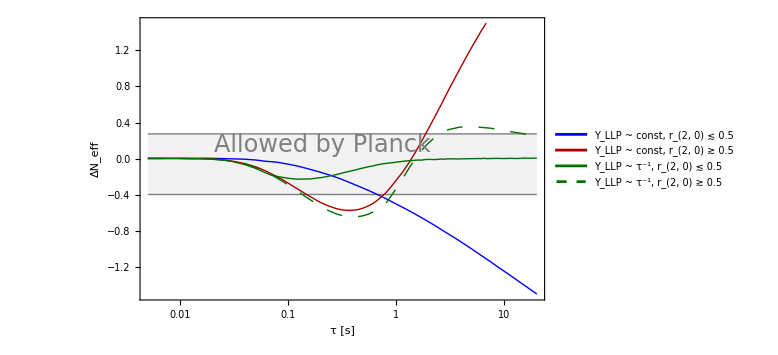

```mathematica
LLPsel="Scalar";
LLPsel2="Toy-pions";
If[Length[OutputLLPUnintegrated[LLPsel]]>2&&Length[OutputLLPUnintegrated[LLPsel2]]>2,
ΔNeffScalarGenericPlot[m_,τ_]=If[τ<0.01,Evaluate[ΔNeffIntegratedInt[LLPsel,m,0.01]],Evaluate[ΔNeffIntegratedInt[LLPsel,m,τ]]];
ΔNeffScalarGenericPlot2[m_,τ_]=If[τ<0.01,Evaluate[ΔNeffIntegratedInt[LLPsel2,m,0.01]],Evaluate[ΔNeffIntegratedInt[LLPsel2,m,τ]]];
NeffSchematic=Show[LogLinearPlot[Evaluate[{ΔNeffMaxPlanck,ΔNeffMinPlanck,ΔNeffScalarGenericPlot[0.03,x],ΔNeffScalarGenericPlot[0.215,x],ΔNeffScalarGenericPlot[0.282,x],ΔNeffScalarGenericPlot[0.23,x]}],{x,0.005,20},FrameStyle->Directive[Thick,Black, 23],Filling->{1->{{2},Directive[Gray,Opacity[0.1]]}},Frame->True,ImageSize->Large,PlotRange->{{0.005,20},{-1.5,1.5}},PlotStyle->{{Thick,Gray},{Thick,Gray},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Darker@Green,Dashing[0.02]}},FrameLabel->{"τ [s]" , "ΔN_eff"}],LogLinearPlot[{2,2,2,2,2,2},{x,0.005,20},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,15]&/@{"Y_LLP ~ const, r_(2, 0) ≲ 0.5","Y_LLP ~ const, r_(2, 0) ≳ 0.5","Y_LLP ~ τ^-1, r_(2, 0) ≲ 0.5","Y_LLP ~ τ^-1, r_(2, 0) ≳ 0.5"},{0.23,0.8}]],Graphics[{Text[Style["Allowed by Planck",24,Gray],Scaled[{0.45,0.55}]]}]];
Export[FileNameJoin[{NotebookDirectory[],"plots/Neff-schematic.pdf"}],NeffSchematic];
NeffSchematic
]
```

## ΔN_eff plot for setups P_decay = 1 and if all processes are included

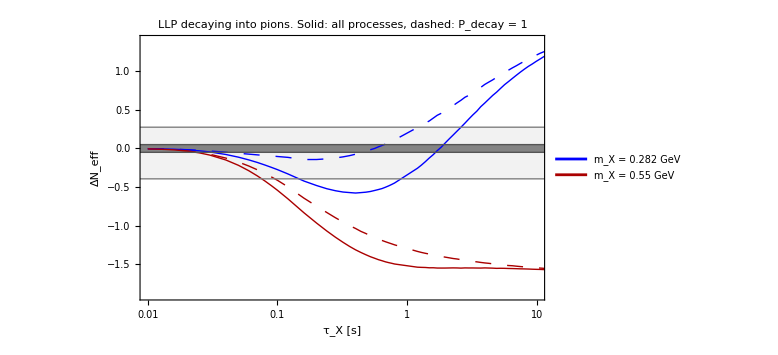

```mathematica
LLPsel="Toy-pions";
LLPsel2="Toy-pions-decay-only";
If[Length[OutputLLPUnintegrated[LLPsel]]>2&&Length[OutputLLPUnintegrated[LLPsel2]]>2,
mass1=0.282;
mass2=0.55;
{selecteddata11,selecteddata12}=Table[Select[OutputLLPUnintegrated[LLPsel],#[[1]]==mass&],{mass,{mass1,mass2}}];
{selecteddata21,selecteddata22}=Table[Select[OutputLLPUnintegrated[LLPsel2],#[[1]]==mass&],{mass,{mass1,mass2}}];
If[selecteddata11!={}&&selecteddata12!={}&&selecteddata21!={}&&selecteddata22!={},
datasets={#[[1]],#[[2]]-3.044}&/@#[[All,{2,-1}]]&/@{selecteddata11,selecteddata12,selecteddata21,selecteddata22};
plotΔNeffToy=Show[ListLogLinearPlot[Evaluate[Join[datasets,{Table[{t,ΔNeffMaxPlanck},{t,0.001,20,0.01}],Table[{t,ΔNeffMinPlanck},{t,0.001,20,0.01}],Table[{t,0.05},{t,0.001,20,0.01}],Table[{t,-0.05},{t,0.001,20,0.01}]}]],Filling->{5->{{6},Directive[Gray,Opacity[0.1]]},7->{{8},Directive[Darker@Gray,Opacity[0.7]]}},FrameStyle->Directive[Thick,Black, 23],Joined->True,Frame->True,ImageSize->Large,PlotRange->{{0.01,10},{-1.9,1.4}},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Gray},{Thick,Gray},{Thick,Darker@Gray},{Thick,Darker@Gray}},FrameLabel->{"τ_X [s]" , "ΔN_eff"},ImageMargins->0,PlotLabel->Style[Row[{NamesLabel[LLPsel],". Solid: all processes, dashed: P_decay = 1"}],18,Black]],LogLinearPlot[{2,2,2,2,2,2},{x,0.005,20},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,18]&/@{"m_X = "<>ToString[mass1]<>" GeV","m_X = "<>ToString[mass2]<>" GeV"},{0.19,0.9}],ImageMargins->0]];
Export[FileNameJoin[{NotebookDirectory[],"plots/Model-independent-mass/DeltaNeffModelIndependent.pdf"}],plotΔNeffToy];
plotΔNeffToy
,
Print["The chosen masses do not exist. Generate data for them or use another masses"]
]
,
Print[Row[{"There is no data for the selected models "<>LLPsel<>"and/or "<>LLPsel2<>". Generate it first!"}]]
]
```

## r_inj

### Definitions

```mathematica
in="r1";
ls="Scalar";
{τminPlot[ls,in],τmaxPlot[ls,in]}={0.01,20.};
{mminPlot[ls,in],mmaxPlot[ls,in]}={0.18,1.8};
rangesContours[ls,in]=Join[{Round[Max[r1minmax[ls]],0.1],Round[Min[r1minmax[ls]],0.0001]},{-2.,-1.,-0.5,-0.3,-0.15,-0.1,-0.03,0.,0.03,0.1,0.2,0.4}]//Sort//DeleteDuplicates;
ContoursMinimal[ls,in]={0.01};
rangesLegend[ls,in]={0.,0.01,0.05,0.1,0.2,0.3,0.4,0.5,0.6};
ls="Toy-pions";
{τminPlot[ls,in],τmaxPlot[ls,in]}={0.02,10.};
{mminPlot[ls,in],mmaxPlot[ls,in]}=mminmax[ls];
rangesContours[ls,in]=Join[{Round[Max[r1minmax[ls]],0.1],Round[Min[r1minmax[ls]],0.0001]},{-2.,-1.,-0.5,-0.3,-0.15,-0.1,-0.03,0.,0.03,0.1,0.2,0.4}]//Sort//DeleteDuplicates;
ContoursMinimal[ls,in]={0.01};
rangesLegend[ls,in]={0.,0.01,0.05,0.1,0.2,0.3,0.4,0.5,0.6};
ls="Toy-pions-decay-only";
{τminPlot[ls,in],τmaxPlot[ls,in]}={0.02,10.};
{mminPlot[ls,in],mmaxPlot[ls,in]}=mminmax[ls];
rangesContours[ls,in]=Join[{Round[Max[r1minmax[ls]],0.1],Round[Min[r1minmax[ls]],0.0001]},{-2.,-1.,-0.5,-0.3,-0.15,-0.1,-0.03,0.,0.03,0.1,0.2,0.4}]//Sort//DeleteDuplicates;
ContoursMinimal[ls,in]={0.01};
rangesLegend[ls,in]={0.,0.01,0.05,0.1,0.2,0.3,0.4,0.5,0.6};
ls="Pure-EM-decay";
{τminPlot[ls,in],τmaxPlot[ls,in]}=τminmax[ls];
{mminPlot[ls,in],mmaxPlot[ls,in]}={Max[Min[mminmax[ls]],0.1],Max[mminmax[ls]]};
rangesContours[ls,in]=Join[{Round[Max[r1minmax[ls]],0.1],Round[Min[r1minmax[ls]],0.0001]},{-2.,-1.,-0.5,-0.3,-0.15,-0.1,-0.03,0.,0.03,0.1,0.2,0.4}]//Sort//DeleteDuplicates;
ContoursMinimal[ls,in]={0.01};
rangesLegend[ls,in]={0,0.01,0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7};
ls="HNL-mixing-mu";
{τminPlot[ls,in],τmaxPlot[ls,in]}=τminmax[ls];
{mminPlot[ls,in],mmaxPlot[ls,in]}={Max[Min[mminmax[ls]],0.1],Max[mminmax[ls]]};
rangesContours[ls,in]=Join[{Round[Max[r1minmax[ls]],0.1],Round[Min[r1minmax[ls]],0.0001]},{-2.,-1.,-0.5,-0.3,-0.15,-0.1,-0.03,0.,0.03,0.1,0.2,0.4}]//Sort//DeleteDuplicates;
ContoursMinimal[ls,in]={0.01};
rangesLegend[ls,in]={0,0.01,0.05,0.1,0.25,0.5,1.};
```

### Plot

```mathematica
in="r1";
Plotrinj[LLPsel_,mlogOption_]:=Block[{},
If[Length[OutputLLPintegrated[LLPsel]]>2,
zmargin=If[LLPsel=="HNL-mixing-mu",0.5,0.1];
colorfunction=Function[{z},Which[z<0.01,White,(*Values less than 0.01 remain white*)0.01<=z<0.05,Blend[{Lighter@LightRed,Lighter@Lighter@Red},Rescale[z,{0.01,0.05}]],0.05<=z<zmargin,Blend[{Lighter@Lighter@Red,Lighter@Red},Rescale[z,{0.05,zmargin}]],zmargin<=z<0.7,Blend[{Lighter@Red,Red},Rescale[z,{0.1,0.7}]],z>=0.7,Red,True,White]]; (*Default to white if out of range*)
pt1=ContourPlot[Evaluate[r1LLP[LLPsel,m,t]],{m,mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},{t,τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]},PlotPoints->200,FrameStyle->Directive[Thick,Black,22],ImageSize->Large,Contours->ContoursMinimal[LLPsel,in],LabelStyle->Directive[18,Black],PlotRange->{{mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},{τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]},All},FrameLabel->{"m [GeV]","τ [s]"},ScalingFunctions->{mlogOption,"Log","Linear"},PlotLabel->Style[Row[{NamesLabel[LLPsel]}],22,Thick,Black],ContourShading->None,ColorFunctionScaling->False,ContourStyle->{{Thick,Black,Dashing[0.02]},{Thick,Black},{Thick,Black,Dashing[0.02]}} (*Define contour line style*)];
contoursranges=Join[ContoursMinimal[LLPsel,in],{0.02,0.03,0.05,0.07,0.1},Table[x,{x,0.11,Max[0.7,Max[r1minmax[ls]]],(Max[0.7,Max[r1minmax[ls]]]-0.11)/40}]];
pt2=ContourPlot[Evaluate[r1LLP[LLPsel,m,t]],{m,mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},{t,τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]},PlotPoints->200,FrameStyle->Directive[Thick,Black,22],ImageSize->Large,ColorFunction->colorfunction,Contours->contoursranges,(*Ensure smooth gradient*)LabelStyle->Directive[18,Black],PlotRange->{{mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},{τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]},All},FrameLabel->{"m [GeV]","τ [s]"},ScalingFunctions->{mlogOption,"Log","Linear"},PlotLabel->Style[Row[{NamesLabel[LLPsel]}],22,Thick,Black],ColorFunctionScaling->False,ContourShading->True,(*Keep the gradient shading*)ContourStyle->None,PlotLegends->BarLegend[{colorfunction,MinMax[rangesLegend[LLPsel,in]]},(*Use the min-max of ranges for the legend*)LabelStyle->Directive[Black,FontSize->16],LegendLabel->Placed[Style["r_inj",FontSize->22],Top],LegendMarkerSize->500(*Make ticks and frame around color bar thicker*)]];
(*Combine pt1 and pt2 and attach a single legend using Legended*)
ptNeff=Legended[Show[pt2,pt1],{}];
Export[FileNameJoin[{NotebookDirectory[],"plots",LLPsel,"rinj-"<>LLPsel<>".png"}],ptNeff,"PNG",ImageResolution->500];
ptNeff
,
Print[Row[{"There is no data for the selected model "<>LLPsel<>". Generate it first!"}]]
]
]
LLPsel="Scalar";
pt1=Plotrinj[LLPsel,"Log"]
```

## r_ν

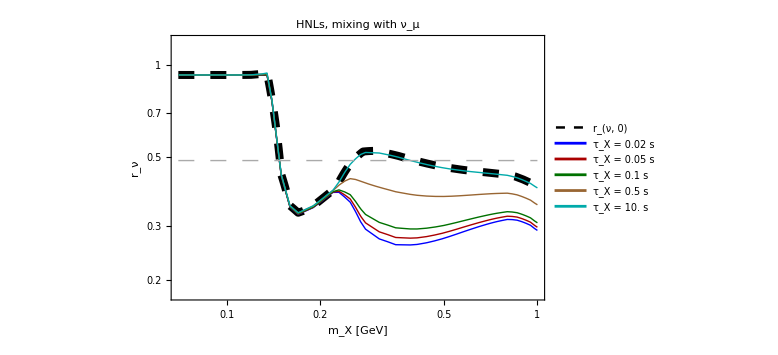

```mathematica
in="rν";
ls="Scalar";
{mminPlot[ls,in],mmaxPlot[ls,in]}={0.21,1.95};
τlistr2[ls]={0.02,0.05,0.1,0.5,10.};
ls="Toy-pions";
{mminPlot[ls,in],mmaxPlot[ls,in]}=mminmax[ls];
τlistr2[ls]={0.02,0.05,0.1,0.5,10.};
ls="Toy-pions-decay-only";
{mminPlot[ls,in],mmaxPlot[ls,in]}=mminmax[ls];
τlistr2[ls]={0.02,0.05,0.1,0.5,10.};
ls="Pure-EM-decay";
{mminPlot[ls,in],mmaxPlot[ls,in]}=mminmax[ls];
τlistr2[ls]={0.02,0.05,0.1,0.5,10.};
ls="HNL-mixing-mu";
{mminPlot[ls,in],mmaxPlot[ls,in]}={0.07,1.};
τlistr2[ls]={0.02,0.05,0.1,0.5,10.};
(*Plot*)
Plotrν[LLPsel_]:=Block[{},
If[Length[OutputLLPintegrated[LLPsel]]>2,
plotr2=Show[LogLogPlot[Evaluate[Join[{EnergyFractionsToν[LLPsel,"Total",m]},Table[r2LLP[LLPsel,m,t],{t,τlistr2[LLPsel]}]]],{m,mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},PlotRange->{{mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},{0.7*Min[r2minmax[LLPsel]],1.2}},PlotStyle->{{Thickness[0.01],Black,Dashing[0.02]},{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Brown},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},PlotLegends->Placed[LineLegend[Style[#,16]&/@Join[{"r_(ν, 0)"},Table[Row[{"τ_X = ",τ," s"}],{τ,τlistr2[LLPsel]}]],LegendLayout->"Row"],{0.3,0.16}],PlotStyle->{{Thick,Gray}},Frame-> True,FrameLabel->{"m_X [GeV]" , "r_ν"},FrameStyle->Directive[Thick,Black, 23],ImageSize->Large,PlotLabel->Style[Row[{NamesLabel[LLPsel]}],18,Black]],LogLogPlot[{21/(22.+21)},{m,mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},PlotRange->{{mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},{0.01,1.1}},PlotStyle->{{Thick,Lighter@Gray,Dashing[0.02]},{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Brown},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Lighter@Lighter@Purple},{Thick,Black},{Thick,Lighter@Lighter@Lighter@Cyan},{Thick, Black,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}}]];
Export[FileNameJoin[{NotebookDirectory[],"plots",LLPsel,"rnu-"<>LLPsel<>"-time-dependent.pdf"}],plotr2];
plotr2
,
Print[Row[{"There is no data for the selected model "<>LLPsel<>". Generate it first!"}]]
]
]
LLPsel="HNL-mixing-mu";
Plotrν[LLPsel]
```

## ΔN_eff

### Definitions

```mathematica
in="dneff";
LLPsel="Scalar";
{τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]}={0.02,10.};
{mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]}={0.18,0.35};
rangesContours[LLPsel,in]=Join[Round[ΔNeffUnintegratedMinMax[LLPsel],0.1],{-2.,-1.,-0.5,-0.3,-0.15,-0.1,-0.03,0.,0.03,0.1,0.2,0.4}]//Sort;
ContoursMinimal[LLPsel,in]={-0.3,0.,0.3};
rangesLegend[LLPsel,in]={-2,-0.5,-0.3,-0.2,-0.1,-0.05,-0.03,0.,0.03,0.1,0.2,0.5};
(*Model-independent-mass*)
Do[
{τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]}=τminmax[LLPsel];
{mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]}=mminmax[LLPsel];
rangesContours[LLPsel,in]=Join[Round[ΔNeffUnintegratedMinMax[LLPsel],0.1],{-1.,-0.5,-0.3,-0.15,-0.1,-0.03,0.,0.03,0.1,0.2}]//Sort;
ContoursMinimal[LLPsel,in]={-0.3,0.,0.3};
rangesLegend[LLPsel,in]={-1.5,-0.5,-0.3,-0.2,-0.1,-0.05,-0.03,0.,0.03,0.1,0.2};
,{LLPsel,{"Toy-pions","Toy-pions-decay-only"}}]
(*Model-independent-mass*)
ln="Pure-EM-decay";
{τminPlot[ln,in],τmaxPlot[ln,in]}=τminmax[ln];
{mminPlot[ln,in],mmaxPlot[ln,in]}={0.5,Max[mminmax[ln]]};
rangesContours[ln,in]=Join[Round[ΔNeffUnintegratedMinMax[ln],0.1],{-1.,-0.5,-0.3,-0.15,-0.1,-0.03,0.}]//DeleteDuplicates//Sort;
ContoursMinimal[ln,in]={ΔNeffMinPlanck,0.,ΔNeffMaxPlanck};
rangesLegend[ln,in]={-1.5,-0.5,-0.3,-0.2,-0.1,-0.05,-0.03,0.};
```

### Plot

```mathematica
in="dneff";
PlotΔNeff[LLPsel_,mlogOption_]:=Module[{ptNeff,pt1,pt2},
If[Length[OutputLLPUnintegrated[LLPsel]]>2,
If[Max[ΔNeffUnintegratedMinMax[LLPsel]]>0,
colorfunction=Function[{z},Which[z<=ΔNeffMinPlanck,Blend[{Blue,Lighter@Lighter@Blue},Rescale[z,{Min[ΔNeffUnintegratedMinMax[LLPsel]],ΔNeffMinPlanck}]],ΔNeffMinPlanck<z<=0.03,Blend[{Lighter@Lighter@Blue,White},Rescale[z,{ΔNeffMinPlanck,-0.03}]],-0.03<z<=0.03,White,(*Intermediate gray region*)z>0.03,Blend[{White,Red},Rescale[z,{0.03,Max[ΔNeffUnintegratedMinMax[LLPsel]]}]]]];
,
colorfunction=Function[{z},Which[z<=ΔNeffMinPlanck,Blend[{Blue,Lighter@Lighter@Blue},Rescale[z,{Min[ΔNeffUnintegratedMinMax[LLPsel]],ΔNeffMinPlanck}]],ΔNeffMinPlanck<z<=0.03,Blend[{Lighter@Lighter@Blue,White},Rescale[z,{ΔNeffMinPlanck,-0.03}]],-0.03<z<=0.03,White,(*Intermediate gray region*)z>0.03,Blend[{White,Red},Rescale[z,{0.03,Max[ΔNeffUnintegratedMinMax[LLPsel]]}]]]];
];
pt1=ContourPlot[Evaluate[ΔNeffUnintegratedInt[LLPsel,m,t]],{m,mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},{t,τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]},PlotPoints->200,FrameStyle->Directive[Thick,Black,22],ImageSize->Large,Contours->ContoursMinimal[LLPsel,in],LabelStyle->Directive[18,Black],PlotRange->{{mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},{τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]},All},FrameLabel->{"m_X [GeV]","τ_X [s]"},ScalingFunctions->{mlogOption,"Log","Linear"},PlotLabel->Style[Row[{NamesLabel[LLPsel]}],22,Thick,Black],ContourShading->None,(*Ensure only contour lines are shown*)ContourStyle->{{Thick,Black,Dashing[0.02]},{Thick,Black},{Thick,Black,Dashing[0.02]}} (*Define contour line style*)];
pt2=ContourPlot[Evaluate[ΔNeffUnintegratedInt[LLPsel,m,t]],{m,mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},{t,τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]},PlotPoints->200,FrameStyle->Directive[Thick,Black,22],ImageSize->Large,ColorFunction->colorfunction,Contours->100,(*Ensure smooth gradient*)LabelStyle->Directive[18,Black],PlotRange->{{mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]},{τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]},All},FrameLabel->{"m_X [GeV]","τ_X [s]"},ScalingFunctions->{mlogOption,"Log","Linear"},PlotLabel->Style[Row[{NamesLabel[LLPsel]}],22,Thick,Black],ColorFunctionScaling->False,ContourShading->True,(*Keep the gradient shading*)ContourStyle->None,PlotLegends->BarLegend[{colorfunction,MinMax[rangesLegend[LLPsel,"dneff"]]},(*Use the min-max of ranges for the legend*)LabelStyle->Directive[Black,FontSize->16],LegendLabel->Placed[Style["ΔN_eff",FontSize->22],Top],LegendMarkerSize->500(*Make ticks and frame around color bar thicker*)]];
(*Combine pt1 and pt2 and attach a single legend using Legended*)
ptNeff=Legended[Show[pt2,pt1],{}];
Export[FileNameJoin[{NotebookDirectory[],"plots",LLPsel,"DeltaNeff-"<>LLPsel<>".png"}],ptNeff,"PNG",ImageResolution->500];
ptNeff
,
Print[Row[{"There is no data for the selected model "<>LLPsel<>". Generate it first!"}]]
]
]
LLPsel="Scalar";
pt1=PlotΔNeff[LLPsel,"Log"]
```

-Graphics-

## Δ(ΔN_eff)

### Definitions

```mathematica
in="ddneff";
LLPsel="Scalar";
{τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]}={0.02,10.};
{mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]}={0.18,0.35};
rangesContours[LLPsel,in]=Join[{-0.5,-0.3,-0.15,-0.1,-0.03,0.}]//Sort;
ContoursMinimal[LLPsel,in]={-0.03,0.};
rangesLegend[LLPsel,in]={-0.5,-0.3,-0.2,-0.1,-0.05,-0.03,0.};
(*Model-independent-mass*)
LLPsel="Toy-pions";
Do[
{τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]}=τminmax[LLPsel];
{mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]}=mminmax[LLPsel];
rangesContours[LLPsel,in]=Join[{-0.15,-0.1,-0.03,0.}]//Sort;
ContoursMinimal[LLPsel,in]={-0.03,0.,0.03};
rangesLegend[LLPsel,in]={-0.2,-0.1,-0.05,-0.03,0.};
,{LLPsel,{"Toy-pions","Toy-pions-decay-only"}}]
(*Model-independent-mass*)
LLPsel="Pure-EM-decay";
{τminPlot[LLPsel,in],τmaxPlot[LLPsel,in]}={Min[τminmax[LLPsel]],0.3};
{mminPlot[LLPsel,in],mmaxPlot[LLPsel,in]}={0.5,Max[mminmax[LLPsel]]};
rangesContours[LLPsel,in]=Join[{-0.1,-0.05,-0.03,0.}]//Sort;
ContoursMinimal[LLPsel,in]={-0.03,0.,0.03};
rangesLegend[LLPsel,in]={-0.1,-0.05,-0.03,0.};
```

### Plot

```mathematica
PlotΔΔNeff[LLPsel_,mlogOption_]:=Module[{pt1,pt2,ptNeff},
If[Length[OutputLLPUnintegrated[LLPsel]]>2&&Length[OutputLLPintegrated[LLPsel]]>2,
If[Max[ΔNeffUnintegratedMinMax[LLPsel]]>0,
colorfunction=Function[{z},Which[z<=-0.03,Blend[{Blue,White},Rescale[z,{Min[rangesContours[LLPsel,"ddneff"]],-0.03}]],-0.03<z<=0.03,White,(*Intermediate gray region*)z>0.03,Blend[{White,Red},Rescale[z,{0.03,Max[rangesContours[LLPsel,"ddneff"]]}]]]];
,
colorfunction=Function[{z},Which[z<=-0.03,Blend[{Blue,White},Rescale[z,{Min[rangesContours[LLPsel,"ddneff"]],-0.03}]],-0.03<z<=0.03,White,(*Intermediate gray region*)z>0.03,Blend[{White,Red},Rescale[z,{0.03,Max[rangesContours[LLPsel,"ddneff"]]}]]]];
];
pt1=ContourPlot[Evaluate[ΔNeffUnintegratedInt[LLPsel,m,t]-ΔNeffIntegratedInt[LLPsel,m,t]],{m,mminPlot[LLPsel,"ddneff"],mmaxPlot[LLPsel,"ddneff"]},{t,τminPlot[LLPsel,"ddneff"],τmaxPlot[LLPsel,"ddneff"]},PlotPoints->200,FrameStyle->Directive[Thick,Black,22],ImageSize->Large,Contours->ContoursMinimal[LLPsel,"ddneff"],LabelStyle->Directive[18,Black],PlotRange->{{mminPlot[LLPsel,"ddneff"],mmaxPlot[LLPsel,"ddneff"]},{τminPlot[LLPsel,"ddneff"],τmaxPlot[LLPsel,"ddneff"]},All},FrameLabel->{"m [GeV]","τ [s]"},ScalingFunctions->{mlogOption,"Log","Linear"}(*,PlotLabel->Style[Row[{LLPsel}],22,Thick,Black]*),ContourShading->None,(*Ensure only contour lines are shown*)ContourStyle->{{Thick,Black,Dashing[0.02]},{Thick,Black},{Thick,Black,Dashing[0.02]}} (*Define contour line style*)];
pt2=ContourPlot[Evaluate[ΔNeffUnintegratedInt[LLPsel,m,t]-ΔNeffIntegratedInt[LLPsel,m,t]],{m,mminPlot[LLPsel,"ddneff"],mmaxPlot[LLPsel,"ddneff"]},{t,τminPlot[LLPsel,"ddneff"],τmaxPlot[LLPsel,"ddneff"]},PlotPoints->200,FrameStyle->Directive[Thick,Black,22],ImageSize->Large,ColorFunction->colorfunction,Contours->100,(*Ensure smooth gradient*)LabelStyle->Directive[18,Black],PlotRange->{{mminPlot[LLPsel,"ddneff"],mmaxPlot[LLPsel,"ddneff"]},{τminPlot[LLPsel,"ddneff"],τmaxPlot[LLPsel,"ddneff"]},All},FrameLabel->{"m [GeV]","τ [s]"},ScalingFunctions->{mlogOption,"Log","Linear"},PlotLabel->Style[Row[{LLPsel}],22,Thick,Black],ColorFunctionScaling->False,ContourShading->True,(*Keep the gradient shading*)ContourStyle->None,PlotLegends->BarLegend[{colorfunction,MinMax[rangesLegend[LLPsel,"ddneff"]]},(*Use the min-max of ranges for the legend*)LabelStyle->Directive[Black,FontSize->16],LegendLabel->Placed[Style[Row[{Subsuperscript["N","eff","unint"],"-",Subsuperscript["N","eff","int"]}],FontSize->22],Top],LegendMarkerSize->500(*Make ticks and frame around color bar thicker*)]];
(*Combine pt1 and pt2 and attach a single legend using Legended*)
ptNeff=Legended[Show[pt2,pt1],{}];
If[LLPsel=="Pure-EM-decay",
Export[FileNameJoin[{NotebookDirectory[],"plots","validation-unintegrated-"<>LLPsel<>".png"}],ptNeff,"PNG",ImageResolution->500]
,
Export[FileNameJoin[{NotebookDirectory[],"plots",LLPsel,"DeltaDeltaNeff-"<>LLPsel<>".png"}],ptNeff,"PNG",ImageResolution->500]];
ptNeff
,
Print[Row[{"There is no data for the selected model "<>LLPsel<>". Generate it first!"}]]
]
]
LLPsel="Pure-EM-decay";
pt1=PlotΔΔNeff[LLPsel,"Log"]
```

# Plots - neutrino distributions

## Importing routines

```mathematica
importDistributionData[model_]:=Block[{file=FileNameJoin[{NotebookDirectory[],"Output",model,"Cluster output/thermodynamics-distribution_"<>model<>".json"}]},
If[FileExistsQ[file],
modeL=model;
dataDistrLLP[modeL]=SortBy[Import[FileNameJoin[{NotebookDirectory[],"Output",model,"Cluster output/thermodynamics-distribution_"<>model<>".json"}],"JSON"],{1,2}];
,
Print[Row[{"The distributions file for the given model ",model, " does not exist. Generate it first using the unintegrated Boltzmann code!"}]]
]
]
{flavorCorrespondence["ν_e"],flavorCorrespondence["ν_μ"],flavorCorrespondence["ν_τ"]}={2,3,4};
ConvertedDistr[LLPsel_,num_,flavor_]:={#[[1]],(#[[1]])^3*#[[flavorCorrespondence[flavor]]]}&/@dataDistrLLP[LLPsel][[num]][[4]];
ConvertedDistrPow[data_,num_,flavor_,pow_]:={#[[1]],(#[[1]])^pow*#[[flavorCorrespondence[flavor]]]}&/@data[[num]][[4]];
(*Block computing mean energy*)
blocke[data_,i_,flavor_]:=Block[{},
{datanum,datae}=ConvertedDistrPow[data,i,flavor,#]&/@{2,3};
maxy=Max[datanum[[All,1]]];
{intnum[x_],inte[x_]}=Interpolation[#,InterpolationOrder->1][x]&/@{datanum,datae};
{data[[i]][[1]],data[[i]][[2]],NIntegrate[inte[x],{x,0.001,maxy},Method->"InterpolationPointsSubdivision"]/NIntegrate[intnum[x],{x,0.001,maxy},Method->"InterpolationPointsSubdivision"]}
]
flavlist={"ν_e","ν_μ","ν_τ"};
{flavorCorrespondence["ν_e"],flavorCorrespondence["ν_μ"],flavorCorrespondence["ν_τ"]}={2,3,4};
```

## Tests

## Importing test data

```mathematica
Print["List of selected models:"]
(*Step 1:Define the file pattern with a wildcard for'model'*)
filePattern=FileNameJoin[{NotebookDirectory[],"Output","*","Cluster output","thermodynamics-distribution_*.json"}];
(*Step 2:Get all files matching the pattern*)
matchingFiles=FileNames[filePattern];
(*Step 3:Extract the'model' from each file path*)
models=matchingFiles/. path_String:>Module[{parts,outputPos},
parts=FileNameSplit[path];
outputPos=First@Flatten@Position[parts,"Output"];
parts[[outputPos+1]]
];
(*Display the list of models*)
uniqueModels
modellist=selectionDialogExplanation[uniqueModels,uniqueModels,"Select the models for which the distribution data will be imported",200]
Do[
model=modelImport;
importDistributionData[modelImport];
mrangedistr[modelImport]=dataDistrLLP[modelImport][[All,1]]//DeleteDuplicates;
τrangedistr[modelImport]=dataDistrLLP[modelImport][[All,2]]//DeleteDuplicates;
mτlists[modelImport]=dataDistrLLP[modelImport][[All,{1,2}]]
,{modelImport,modellist}]
mpositions[model_,m_]:=If[MemberQ[mrangedistr[model],m],Position[mτlists[model],m][[All,1]]//MinMax]
mτposition[model_,m_,τ_]:=Block[{},
mposition=mpositions[model,m];
τposition=Position[τrangedistr[model],τ][[1]][[1]]-1;
mposition[[1]]+τposition
]
```

## Computing N_eff by integrating the tabulated distributions

```mathematica
ρsFinalDistr[model_,m_]:=Module[{int,datt,ρνFinal,dat0,TEMfinal,ρEMfinal,ρνFinalInt,fνint,fνdatt,ρνlist,mass,lifetime,margin=10^-5,afinal,atTdata,distrdata,fνp3datt,fνp3int,positions,dataini={{0,0,0,0,0,0,0,0}}},
If[MemberQ[mrangedistr[model],m],
positions=mpositions[model,m];
Do[
dat0=dataDistrLLP[model][[pos]];
(*Extracting the {a,t,T} table and {p,Subscript[fν, e],Subscript[fν, μ],Subscript[fν, τ]} table - the same as generated by the python code*)
{atTdata,distrdata}={dat0[[-2]],dat0[[-1]]};
{mass,lifetime}=dat0[[#]]&/@{1,2};
(*Extracting the final values of the scale factor and temperature from the {a,t,T} table*)
{afinal,TEMfinal}=atTdata[[-1]][[#]]&/@{1,-1};
(*Calculating the energy density of photons*)
ρEMfinal=2*Pi^2/30 TEMfinal^4;
(*Calculating neutrino energy densities*)
Do[
(*Tabulated data {Subscript[p, physical],Subscript[f, Subscript[ν, α]]}*)
fνdatt[flavor]={#[[1]],#[[2]]}&/@(distrdata[[All,{1,flavorCorrespondence[flavor]}]]);
(*Tabulated data {Subscript[p, physical],Subscript[f, Subscript[ν, α]]*Subscript[p^3, physical]}*)
fνp3datt[flavor]={#[[1]],#[[2]]*(#[[1]])^3}&/@fνdatt[flavor];
(*Maximal value*)
valmax=Max[fνp3datt[flavor][[All,-1]]];
effxmax=Select[fνp3datt[flavor],#[[2]]>margin*valmax&][[-1]][[1]];
(*Logarithmic interpolation to avoid the wiggles*)
fνp3int[flavor,x_]=Interpolation[Log[fνp3datt[flavor]],InterpolationOrder->1][Log[x]]//Exp;
(*fνint[flavor,x_]=Interpolation[fνdatt[flavor],InterpolationOrder->1][x];*)
(*The integral defining the neutrino energy density Subscript[ρ, Subscript[ν, α]]*)

(*ρνFinalInt[flavor]=2*(4Pi)/(2Pi)^3*Quiet[NIntegrate[fνp3int[flavor,x],{x,Min[fνdatt[flavor][[All,1]]],effxmax},Method->"InterpolationPointsSubdivision"]];*)
ρνFinalInt[flavor]=Re[2*(4Pi)/(2Pi)^3*Quiet[NIntegrate[fνp3int[flavor,Exp[x]]Exp[x],{x,Log[Min[fνdatt[flavor][[All,1]]]],Log[effxmax]},Method->"InterpolationPointsSubdivision"]]];
,{flavor,flavlist}];
ρνlist=ρνFinalInt[#]&/@flavlist;
NeffVal=8/7(11/4)^(4/3)Total[ρνlist]/ρEMfinal;
dataini=Join[dataini,{Join[{m,lifetime,NeffVal,NeffUnintegratedInt[model,mass,lifetime],ρEMfinal},ρνlist,Table[fνp3datt[flavor],{flavor,flavlist}],Table[fνp3int[flavor,x],{flavor,flavlist}]]}]
,{pos,positions[[1]],positions[[2]]}];
Drop[dataini,1]
,
Print[Row[{"The data does not exist for the following mass ",m," GeV. Allowed masses (in GeV): ", mrangedistr[model]}]]
]
]
ΔNeffPlot[model_,m_]:=Block[{},
If[MemberQ[mrangedistr[model],m],
tabbb[x_]=ρsFinalDistr[model,m];
dataNeff=tabbb[x][[All,{2,#}]]&/@{3,4};
dataΔNeff={#[[2]],#[[3]]-#[[4]]}&/@tabbb[x];
pt1=ListLogLinearPlot[dataΔNeff,Joined->True,Frame->True,FrameStyle->Directive[Thick,Black,22],FrameLabel->{"τ [s]","N_eff[M]-N_eff[P]"},ImageSize->Large,PlotLabel->Style[Row[{"model",model,", m = ",m," GeV"}],18,Black],PlotRange->{MinMax[τrangedistr[model]],All}];
pt2=ListLogLinearPlot[dataNeff,Joined->True,PlotRange->{MinMax[τrangedistr[model]],All},Frame->True,FrameStyle->Directive[Thick,Black,22],FrameLabel->{"τ [s]","N_eff"},ImageSize->Large,PlotLegends->Placed[Style[#,18,Black]&/@{"Mathematica","python"},{0.2,0.2}],PlotLabel->Style[Row[{"m = ",m," GeV"}],18,Black]];
Style[Row[{pt1,pt2}],ImageSizeMultipliers->{1, 1}]
,
Print[Row[{"The data does not exist for the following mass ",m," GeV. Allowed masses (in GeV): ", mrangedistr[model]}]]
]
]
ΔNeffPlot[modellist[[1]],0.282]
```

```mathematica
ListIntegrate
```

## Computing the mean energies of neutrinos

```mathematica
EmeanFinalDistr[model_,m_]:=Module[{int,datt,ρνFinal,dat0,TEMfinal,ρEMfinal,ρνFinalInt,fνint,fνdatt,ρνlist,mass,lifetime,margin=10^-5,afinal,atTdata,distrdata,fνp3datt,fνp3int,positions,EνFinalInt,distrnull={{1,1,1,1,1}}},
If[MemberQ[mrangedistr[model],m],
positions=mpositions[model,m];
Do[
dat0=dataDistrLLP[model][[pos]];
lifetime=dat0[[2]];
(*Extracting the {a,t,T} table and {p,Subscript[fν, e],Subscript[fν, μ],Subscript[fν, τ]} table - the same as generated by the python code*)
{atTdata,distrdata}={dat0[[-2]],dat0[[-1]]};
(*Extracting the final values of the scale factor and temperature from the {a,t,T} table*)
{afinal,TEMfinal}=atTdata[[-1]][[#]]&/@{1,-1};
(*Calculating the energy density of photons*)
ρEMfinal=2*Pi^2/30 TEMfinal^4;
(*Calculating neutrino energy densities*)
Do[
(*Tabulated data {Subscript[p, physical],Subscript[f, Subscript[ν, α]]}*)
fνdatt[flavor]={#[[1]],#[[2]]}&/@(distrdata[[All,{1,flavorCorrespondence[flavor]}]]);
(*Tabulated data {Subscript[p, physical],Subscript[f, Subscript[ν, α]]*Subscript[p^3, physical]}*)
fνp3datt[flavor]={#[[1]],#[[2]]*(#[[1]])^3}&/@fνdatt[flavor];
(*Maximal value*)
valmax=Max[fνp3datt[flavor][[All,-1]]];
effxmax=Select[fνp3datt[flavor],#[[2]]>margin*valmax&][[-1]][[1]];
(*Logarithmic interpolation to avoid the wiggles*)
fνint[flavor,x_]=Interpolation[Log[fνdatt[flavor]],InterpolationOrder->1][Log[x]]//Exp;
(*fνint[flavor,x_]=Interpolation[fνdatt[flavor],InterpolationOrder->1][x];*)
(*The integral defining the mean neutrino energy*)
EνFinalInt[flavor]=Re[Quiet[NIntegrate[fνint[flavor,Exp[x]]Exp[x]*Exp[3*x],{x,Log[Min[fνdatt[flavor][[All,1]]]],Log[effxmax]},Method->"InterpolationPointsSubdivision"]](*/Quiet[NIntegrate[fνint[flavor,Exp[x]]Exp[x]*Exp[2*x],{x,Log[Min[fνdatt[flavor][[All,1]]]],Log[effxmax]},Method->"InterpolationPointsSubdivision"]]*)];
,{flavor,flavlist}];
distrnull=Join[distrnull,{Join[{m,lifetime},Table[EνFinalInt[flavor],{flavor,flavlist}]]}];
,{pos,positions[[1]],positions[[2]]}];
SortBy[Drop[distrnull,1],{#[[1]],#[[2]]}&]//Developer`ToPackedArray
,
Print[Row[{"The data does not exist for the following mass ",m," GeV. Allowed masses (in GeV): ", mrangedistr[model]}]]
]
]
flavchoice="ν_μ";
masslistEmean={0.282,0.222,0.55};
Do[
dataEmeanForPaper[model,mass]=EmeanFinalDistr[model,mass];
,{model,modellist},{mass,masslistEmean}]//AbsoluteTiming
```

```mathematica
(*PlotEaverage=ListLogLinearPlot[Evaluate[{EmeanMass1int[τX],EmeanMass2int[τX]}],{τX,0.01,12},Frame->True,ImageSize->Large,FrameStyle->Directive[Black,Thick, 23],PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]}},PlotLegends->Placed[Style[#,18]&/@{"m_X = "<>ToString[mass1]<>" GeV","m_X = "<>ToString[mass2]<>" GeV"},{0.19,0.9}],FrameLabel->{"τ_X [s]","<E_ν>/<E_ν>_P_decay"},PlotRange->{{0.01,12},{0.9,1.03}},PlotLabel->Style[Row[{"flavor ",flavchoice}],18,Black]];
Export[FileNameJoin[{NotebookDirectory[],"plots/Model-independent-mass/EmeanRatiosModelIndependent.pdf"}],PlotEaverage];*)
```

```mathematica
ListLogLinearPlot[(dataEmeanForPaper[#[[1]],#[[2]]][[All,{2,3}]])&/@{{"Scalar",0.222},{"Toy-pions",0.282},{"Toy-pions-decay-only",0.282}},Joined->True,ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,18]]
```

```mathematica
fνρDataExtractor[model_,m_]:=Module[{int,datt,ρνFinal,dat0,TEMfinal,ρEMfinal,ρνFinalInt,fνint,fνdatt,ρνlist,mass,lifetime,margin=10^-5,afinal,atTdata,distrdata,fνp3datt,fνp3int,positions,EνFinalInt,distrnull={{1,1,1,1}}},
If[MemberQ[mrangedistr[model],m],
positions=mpositions[model,m];
Do[
dat0=dataDistrLLP[model][[pos]];
lifetime=dat0[[2]];
(*Extracting the {a,t,T} table and {p,Subscript[fν, e],Subscript[fν, μ],Subscript[fν, τ]} table - the same as generated by the python code*)
{atTdata,distrdata}={dat0[[-2]],dat0[[-1]]};
(*Extracting the final values of the scale factor and temperature from the {a,t,T} table*)
{afinal,TEMfinal}=atTdata[[-1]][[#]]&/@{1,-1};
(*Calculating the energy density of photons*)
ρEMfinal=2*Pi^2/30 TEMfinal^4;
(*Calculating neutrino energy densities*)
Do[
(*Tabulated data {Subscript[p, physical],Subscript[f, Subscript[ν, α]]}*)
fνdatt[flavor]={#[[1]],#[[2]]}&/@(distrdata[[All,{1,flavorCorrespondence[flavor]}]]);
,{flavor,flavlist}];
distrnull=Join[distrnull,{Join[{m,lifetime,ρEMfinal},Table[fνdatt[flavor],{flavor,flavlist}]]}];
,{pos,positions[[1]],positions[[2]]}];
SortBy[Drop[distrnull,1],{#[[1]],#[[2]]}&]//Developer`ToPackedArray
,
Print[Row[{"The data does not exist for the following mass ",m," GeV. Allowed masses (in GeV): ", mrangedistr[model]}]]
]
]
extractedDistrs=fνρDataExtractor["Toy-pions",0.282];
```

```mathematica
integratorSimpson[list_,power_]:=Module[{n=Length[list],sum=0.0},(*list={{x1,f1},{x2,f2},...,{xN,fN}},N must be odd*)
If[OddQ[n]==False,list=Drop[list,-1]];
(*Accumulate integrals in sub-windows of length 2 (3 points).Indices:(2j-1,2j,2j+1).*)
Do[
Module[{pLeft,pMid,pRight,fLeft,fMid,fRight,dx,xMid,xRight},
pLeft=list[[2 j-1,1]];
fLeft=list[[2 j-1,2]];
pMid=list[[2 j,1]];
fMid=list[[2 j,2]];
pRight=list[[2 j+1,1]];
fRight=list[[2 j+1,2]];
dx=pRight-pLeft;  (*step from left to right over two intervals*)
(*Composite Simpson for p^3 f(p):Integral~(dx/6)[pLeft^3*fLeft+4 pMid^3*fMid+pRight^3*fRight]*)
sum+=(dx/6.0)*(pLeft^power*fLeft+4.0*pMid^power*fMid+pRight^power*fRight);
]
,{j,1,(n-1)/2}];
sum];
NeffCalculator[model_,m_]:=Module[{tabbb={Table[1.,9]},ρνe,ρνμ,ρντ,Neff,NeffUnint},
If[MemberQ[mrangedistr[model],m],
extractedDistrs=fνρDataExtractor[model,m];
Do[
Module[{mass,lifetime},
{mass,lifetime}=extractedDistrs[[i]][[#]]&/@{1,2};
{ρνe,ρνμ,ρντ}=(2*(4Pi)/(2Pi)^3*integratorSimpson[extractedDistrs[[i]][[#]],3])&/@Range[4,6];
Neff=8/7(11/4)^(4/3)({ρνe,ρνμ,ρντ}//Total)/(extractedDistrs[[i]][[3]]);
NeffUnint=NeffUnintegratedInt[model,mass,lifetime];
tabbb=Join[tabbb,{Join[{mass,lifetime,extractedDistrs[[i]][[3]],ρνe,ρνμ,ρντ,Neff,NeffUnint,Neff-NeffUnint}]}];
]
,{i,1,Length[extractedDistrs],1}];
Drop[tabbb,1]
,
Print[Row[{"The data does not exist for the following mass ",m," GeV. Allowed masses (in GeV): ", mrangedistr[model]}]]
]
]
```

```mathematica
neffdata=NeffCalculator["Toy-pions",0.282];
pt1=ListLogLinearPlot[neffdata[[All,{2,-1}]],Joined->True,Frame->True,ImageSize->Large,FrameStyle->Directive[Thick,Black,20],FrameLabel->{"τ [s]","N_eff[M]-N_eff[P]"},PlotRange->{MinMax[neffdata[[All,2]]],All},PlotStyle->({Thick,#}&/@{Blue,Darker@Red})];
pt2=ListLogLinearPlot[neffdata[[All,{2,#}]]&/@{-3,-2},Joined->True,Frame->True,ImageSize->Large,FrameStyle->Directive[Thick,Black,20],FrameLabel->{"τ [s]","N_eff"},PlotLegends->Placed[Style[#,20,Black]&/@{"Mathematica","python"},{0.2,0.86}],PlotRange->{MinMax[neffdata[[All,2]]],All},PlotStyle->({Thick,#}&/@{Blue,Darker@Red})];
Style[Row[{pt1,pt2}],ImageSizeMultipliers->{1, 1}]
```

```mathematica
EmeanCalculator[model_,m_]:=Module[{tabbb={Table[1.,3]},ρνe,ρνμ,ρντ,Emean,nνe,nνμ,nντ},
If[MemberQ[mrangedistr[model],m],
extractedDistrs=fνρDataExtractor[model,m];
Do[
Module[{mass,lifetime},
{mass,lifetime}=extractedDistrs[[i]][[#]]&/@{1,2};
{ρνe,ρνμ,ρντ}=(2*(4Pi)/(2Pi)^3*integratorSimpson[extractedDistrs[[i]][[#]],3])&/@Range[4,6];
{nνe,nνμ,nντ}=(2*(4Pi)/(2Pi)^3*integratorSimpson[extractedDistrs[[i]][[#]],2])&/@Range[4,6];
tabbb=Join[tabbb,{Join[{mass,lifetime},{ρνe,ρνμ,ρντ}/{nνe,nνμ,nντ}]}];
]
,{i,1,Length[extractedDistrs],1}];
Drop[tabbb,1]
,
Print[Row[{"The data does not exist for the following mass ",m," GeV. Allowed masses (in GeV): ", mrangedistr[model]}]]
]
]
masslistEmean={0.282,0.55};
modellistEmean={"Toy-pions","Toy-pions-decay-only"};
Do[
EmeanData[mass,model]=EmeanCalculator[model,mass]
,{mass,masslistEmean},{model,modellistEmean}]//AbsoluteTiming;
Do[
dataEmeanRatioForPaper[mass]={#[[2]],(#[[3]])/(#[[5+3]]),(#[[4]])/(#[[5+4]]),(#[[5]])/(#[[5+5]])}&/@Join[EmeanData[mass,modellistEmean[[1]]],EmeanData[mass,modellistEmean[[2]]],2];
,{mass,masslistEmean}
]
ptflav[flav_]:=ListLogLinearPlot[(dataEmeanRatioForPaper[#][[All,{1,flavorCorrespondence[flav]}]])&/@{0.282,0.55},Joined->True,Frame->True,ImageSize->Large,FrameStyle->Directive[Thick,Black,20],FrameLabel->{"τ_X [s]","<E_ν_α>/<E_ν_α>_P_dec"},PlotStyle->({Thick,#}&/@{Blue,Darker@Red}),PlotLegends->Placed[Style[Row[{"m_X = ",#," GeV"}],20,Black]&/@masslistEmean,{0.2,0.2}],PlotLabel->Style[Row[{"Flavor ",flav}],18,Black]]
Style[Row[ptflav[#]&/@{"ν_e","ν_μ","ν_τ"}],ImageSizeMultipliers->{1,1,1}]
Export[FileNameJoin[{NotebookDirectory[],"plots","EmeanRatiosModelIndependent.pdf"}],ptflav["ν_μ"]]
```

## Test

```mathematica
(*importDistributionData["Scalar"]
num=1900;
{dataDistrLLP["Scalar"][[num]][[1]],dataDistrLLP["Scalar"][[num]][[2]]}
num=1000;
{dataDistrLLP["Scalar"][[num]][[1]],dataDistrLLP["Scalar"][[num]][[2]]}
num1=1;
num2=1900;
num3=1868;
LLPsel="Scalar";
ConvertedDistr[LLPsel_,num_,flavor_]:={#[[1]],(#[[1]])^3*#[[flavorCorrespondence[flavor]]]}&/@dataDistrLLP[LLPsel][[num]][[4]];
PlotDistr[LLPsel_,numlist_,flavor_]:=
ListLogLogPlot[Evaluate[ConvertedDistr[LLPsel,#,flavor]&/@numlist],Joined->True,Frame->True,ImageSize->Large,FrameStyle->Directive[Black,Thick, 18],PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Green}},PlotLegends->Placed[Style[#,15]&/@Evaluate[Row[{"m_S = ",dataDistrLLP[LLPsel][[#]][[1]]," GeV, τ_S = ",dataDistrLLP[LLPsel][[#]][[2]]," s"}]&/@numlist],{0.24,0.2}],FrameLabel->{"y [MeV]","y^3f_ν(y) [units]"},PlotRange->{{0.005,2.2},{10^-11,10^-5}},PlotLabel->Style[Row[{NamesLabel[LLPsel], ", flavor ",flavor}],18,Black]]
PlotDistr["Scalar",{num1,num2,num3},"ν_μ"]*)
```

## Toy model - comparing result for the case P_decay = 1 and if allowing other interactions

```mathematica
importDistributionData["Toy-pions"]
importDistributionData["Toy-pions-decay-only"]
(*PlotDistrModelIndependent[numlist1_,numlist2_,flavor_]:=
ListLogLogPlot[Evaluate[Join[ConvertedDistr["Toy-pions",#,flavor]&/@numlist1,ConvertedDistr["Toy-pions-decay-only",#,flavor]&/@numlist2]],Joined->True,Frame->True,ImageSize->Large,FrameStyle->Directive[Black,Thick, 18],PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]}},PlotLegends->Placed[Style[#,15]&/@Evaluate[Row[{"m_S = ",dataDistrLLP["Toy-pions"][[#]][[1]]," GeV, τ_S = ",dataDistrLLP["Toy-pions"][[#]][[2]]," s"}]&/@numlist1],{0.24,0.2}],FrameLabel->{"y [MeV]","y^3f_ν(y) [units]"},PlotRange->{{0.005,0.6},{10^-9,10^-5}},PlotLabel->Style[Row[{NamesLabel[LLPsel], ", flavor ",flavor}],18,Black]];
numlist1={25,24};
numlist2={25,24};
PlotDistrModelIndependent[numlist1,numlist2,"ν_μ"]*)
flavchoice="ν_μ";
mass1=0.282;
mass2=0.55;
If[Length[dataDistrLLP["Toy-pions"]]>2&&Length[dataDistrLLP["Toy-pions-decay-only"]]>2,
Do[
datadistr[llp]=Select[dataDistrLLP[llp],#[[1]]==mass1||#[[1]]==mass2&];
,{llp,{"Toy-pions","Toy-pions-decay-only"}}
];
If[Min[Flatten[Table[Length[Select[dataDistrLLP[llp],#[[1]]==m&]],{m,{mass1,mass2}},{llp,{"Toy-pions","Toy-pions-decay-only"}}]]]>0,
{Emean["Toy-pions"],Emean["Toy-pions-decay-only"]}=Table[blocke[datadistr[#],i,flavchoice],{i,1,Length[datadistr[#]]}]&/@{"Toy-pions","Toy-pions-decay-only"};
{EmeanMass1int[τX_],EmeanMass2int[τX_]}={(Interpolation[Select[Emean["Toy-pions"],#[[1]]==mass1&][[All,{2,3}]],InterpolationOrder->1][τX])/(Interpolation[Select[Emean["Toy-pions-decay-only"],#[[1]]==mass1&][[All,{2,3}]],InterpolationOrder->1][τX]),(Interpolation[Select[Emean["Toy-pions"],#[[1]]==mass2&][[All,{2,3}]],InterpolationOrder->1][τX])/(Interpolation[Select[Emean["Toy-pions-decay-only"],#[[1]]==mass2&][[All,{2,3}]],InterpolationOrder->1][τX])};
(*ListLogLogPlot[Evaluate[{Select[Emean["Toy-pions"],#[[1]]==0.282&][[All,{2,3}]],Select[Emean["Toy-pions"],#[[1]]==0.55&][[All,{2,3}]],Select[Emean["Toy-pions-decay-only"],#[[1]]==0.282&][[All,{2,3}]],Select[Emean["Toy-pions-decay-only"],#[[1]]==0.55&][[All,{2,3}]]}],Joined->True,Frame->True]*)
PlotEaverage=LogLinearPlot[Evaluate[{EmeanMass1int[τX],EmeanMass2int[τX]}],{τX,0.01,12},Frame->True,ImageSize->Large,FrameStyle->Directive[Black,Thick, 23],PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]}},PlotLegends->Placed[Style[#,18]&/@{"m_X = "<>ToString[mass1]<>" GeV","m_X = "<>ToString[mass2]<>" GeV"},{0.19,0.9}],FrameLabel->{"τ_X [s]","<E_ν>/<E_ν>_P_decay"},PlotRange->{{0.01,12},{0.9,1.03}},PlotLabel->Style[Row[{"flavor ",flavchoice}],18,Black]];
Export[FileNameJoin[{NotebookDirectory[],"plots/Model-independent-mass/EmeanRatiosModelIndependent.pdf"}],PlotEaverage];
PlotEaverage
,
Print[Row[{"No masses "<>ToString[mass1]<>" GeV and/or "<>ToString[mass2]<>" GeV available"}]]
]
,
Print[Row[{"No data for the models available"}]]
]
```

# Deleting generated cells

```mathematica
FrontEndTokenExecute["DeleteGeneratedCells"];
FrontEndTokenExecute["SelectAll"];
FrontEndTokenExecute["SelectionCloseAllGroups"];
```